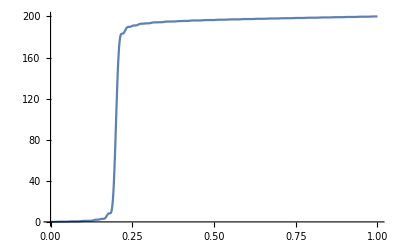

```mathematica
F[a_,L_,L1_,N_,x_]:=(4×a^2)/L^2×(N×x+∑_(k1=2)^N (∑_(k2=1)^(k1-1) ((2×L)/((k1-k2)×π)×Cos[((k1-k2)×π×L1)/L]×Sin[((k1-k2)×π×x)/L]))+∑_(k1=1)^N (∑_(k2=1)^N (L/((k1+k2)×π)×Cos[((k1-k2)×π×L1)/L]×Sin[((k1+k2)×π×x)/L]))+∑_(k=1)^N (x×Cos[(2×k×π×L1)/L])+∑_(k1=2)^N (∑_(k2=1)^(k1-1) ((2×L)/((k1-k2)×π)×Cos[((k1+k2)×π×L1)/L]×Sin[((k1-k2)×π×x)/L]))+∑_(k1=1)^N (∑_(k2=1)^N (L/((k1+k2)×π)×Cos[((k1+k2)×π×L1)/L]×Sin[((k1+k2)×π×x)/L])))
p1=Plot[F[1,1,1/5,50,x],{x,0,1}]
```

```mathematica
b=Table[x,{x,0,1,0.001}];
```

```mathematica
a1=Table[F[1,1,1/5,50,x],{x,0,1,0.001}]
```

{0.,1.77495×10^-7,5.62151×10^-6,0.0000419598,0.000172606,0.000510659,0.00122335,0.00252803,0.0046796,0.0079506,0.0126058,0.0188738,0.0269198,0.0368206,0.0485478,0.0619583,0.076796,0.0927042,0.109246,0.125937,0.142276,0.157785,0.172042,0.184713,0.195572,0.20451,0.211542,0.216789,0.220464,0.222839,0.224217,0.2249,0.22516,0.225215,0.225219,0.225255,0.225346,0.225469,0.22558,0.225643,0.225656,0.225674,0.225834,0.226353,0.227531,0.229733,0.233358,0.238809,0.246449,0.256558,0.269297,0.284675,0.302534,0.322543,0.344211,0.366916,0.389947,0.412555,0.434009,0.453654,0.470959,0.485563,0.497293,0.506173,0.512415,0.516387,0.51857,0.519505,0.519736,0.519753,0.519944,0.520568,0.521729,0.523391,0.525392,0.527492,0.529424,0.530951,0.531932,0.532367,0.532439,0.532526,0.5332,0.535187,0.539316,0.546449,0.557386,0.572784,0.59307,0.618376,0.64849,0.682846,0.720543,0.760392,0.801004,0.840891,0.878591,0.912783,0.942407,0.966756,0.985531,0.998875,1.00734,1.01186,1.01359,1.01388,1.01403,1.01525,1.01847,1.02426,1.03279,1.04379,1.05665,1.07041,1.084,1.09631,1.10642,1.11372,1.11807,1.11989,1.12017,1.1205,1.12289,1.12971,1.14338,1.16619,1.20004,1.24621,1.30513,1.37631,1.45825,1.54851,1.64387,1.74055,1.83451,1.92182,1.99902,2.06346,2.11358,2.14911,2.17116,2.18212,2.18556,2.18583,2.18771,2.19588,2.21452,2.24672,2.29421,2.35705,2.43355,2.52037,2.61282,2.70532,2.79201,2.8675,2.92757,2.96992,2.99467,3.00485,3.00644,3.00821,3.02131,3.05839,3.13261,3.25639,3.44011,3.6908,4.01101,4.39799,4.84326,5.33264,5.84697,6.36326,6.85657,7.30224,7.67861,7.96988,8.16894,8.28013,8.32137,8.32581,8.34254,8.43632,8.68631,9.18363,10.028,11.3232,13.1725,15.6726,18.9085,22.948,27.8367,33.594,40.2104,47.646,55.8303,64.6639,74.0213,83.756,93.7055,103.698,113.56,123.122,132.227,140.738,148.538,155.541,161.691,166.96,171.356,174.911,177.686,179.76,181.23,182.201,182.781,183.079,183.194,183.217,183.221,183.265,183.391,183.621,183.963,184.413,184.952,185.555,186.194,186.838,187.457,188.026,188.526,188.944,189.276,189.521,189.688,189.79,189.841,189.859,189.862,189.864,189.879,189.915,189.979,190.07,190.187,190.324,190.473,190.625,190.772,190.905,191.018,191.108,191.173,191.215,191.237,191.245,191.246,191.247,191.257,191.281,191.325,191.392,191.482,191.595,191.728,191.874,192.03,192.187,192.339,192.48,192.606,192.712,192.798,192.862,192.906,192.933,192.947,192.952,192.952,192.953,192.957,192.967,192.985,193.011,193.043,193.081,193.122,193.163,193.202,193.236,193.264,193.284,193.297,193.303,193.306,193.306,193.307,193.312,193.324,193.345,193.376,193.42,193.474,193.54,193.613,193.693,193.775,193.857,193.936,194.008,194.071,194.125,194.167,194.198,194.22,194.233,194.24,194.242,194.242,194.243,194.245,194.249,194.257,194.269,194.284,194.3,194.317,194.334,194.349,194.362,194.371,194.377,194.38,194.381,194.381,194.382,194.385,194.392,194.405,194.425,194.451,194.486,194.527,194.575,194.627,194.682,194.738,194.792,194.844,194.89,194.931,194.964,194.991,195.01,195.024,195.032,195.036,195.037,195.037,195.037,195.039,195.041,195.046,195.052,195.06,195.068,195.077,195.085,195.092,195.097,195.1,195.102,195.102,195.102,195.103,195.105,195.11,195.119,195.132,195.151,195.175,195.205,195.239,195.277,195.319,195.361,195.403,195.444,195.482,195.516,195.545,195.569,195.587,195.601,195.61,195.615,195.618,195.619,195.619,195.619,195.62,195.621,195.624,195.628,195.632,195.637,195.642,195.646,195.649,195.651,195.652,195.652,195.653,195.653,195.654,195.658,195.664,195.674,195.688,195.706,195.729,195.755,195.785,195.818,195.852,195.887,195.921,195.954,195.984,196.01,196.032,196.05,196.064,196.074,196.081,196.085,196.087,196.087,196.087,196.087,196.088,196.089,196.091,196.093,196.096,196.099,196.101,196.103,196.105,196.105,196.105,196.105,196.106,196.107,196.109,196.114,196.122,196.132,196.146,196.164,196.186,196.21,196.237,196.266,196.296,196.325,196.354,196.381,196.405,196.427,196.444,196.459,196.47,196.477,196.482,196.485,196.487,196.487,196.487,196.487,196.488,196.489,196.49,196.491,196.493,196.494,196.496,196.497,196.497,196.497,196.497,196.498,196.498,196.5,196.504,196.51,196.518,196.529,196.544,196.561,196.582,196.605,196.629,196.655,196.682,196.708,196.733,196.756,196.776,196.794,196.808,196.82,196.829,196.835,196.839,196.841,196.842,196.843,196.843,196.843,196.843,196.844,196.844,196.845,196.846,196.847,196.848,196.848,196.848,196.848,196.849,196.849,196.851,196.853,196.858,196.864,196.874,196.886,196.9,196.917,196.937,196.959,196.982,197.006,197.029,197.052,197.074,197.094,197.112,197.127,197.139,197.149,197.156,197.161,197.164,197.166,197.167,197.167,197.167,197.167,197.167,197.168,197.168,197.169,197.17,197.17,197.17,197.17,197.17,197.17,197.171,197.172,197.174,197.178,197.183,197.19,197.2,197.213,197.227,197.245,197.264,197.284,197.306,197.328,197.35,197.37,197.39,197.407,197.423,197.436,197.446,197.454,197.46,197.464,197.467,197.468,197.469,197.469,197.469,197.469,197.47,197.47,197.47,197.47,197.471,197.471,197.471,197.471,197.471,197.471,197.472,197.474,197.477,197.481,197.487,197.495,197.506,197.519,197.534,197.55,197.569,197.589,197.609,197.63,197.65,197.669,197.686,197.702,197.715,197.727,197.736,197.743,197.748,197.751,197.753,197.754,197.755,197.755,197.755,197.755,197.755,197.755,197.755,197.756,197.756,197.756,197.756,197.756,197.756,197.757,197.758,197.76,197.764,197.769,197.775,197.784,197.795,197.809,197.824,197.84,197.859,197.878,197.897,197.916,197.935,197.952,197.968,197.982,197.994,198.004,198.012,198.018,198.022,198.025,198.026,198.027,198.028,198.028,198.028,198.028,198.028,198.028,198.028,198.028,198.028,198.028,198.028,198.029,198.029,198.03,198.032,198.034,198.038,198.044,198.052,198.061,198.073,198.086,198.102,198.118,198.136,198.154,198.173,198.191,198.208,198.224,198.239,198.251,198.262,198.271,198.278,198.283,198.286,198.289,198.29,198.291,198.291,198.291,198.291,198.291,198.291,198.291,198.291,198.291,198.291,198.291,198.292,198.292,198.292,198.294,198.296,198.299,198.304,198.311,198.319,198.329,198.341,198.355,198.37,198.387,198.404,198.422,198.44,198.457,198.473,198.488,198.501,198.512,198.522,198.53,198.536,198.54,198.543,198.545,198.546,198.547,198.547,198.547,198.547,198.547,198.547,198.547,198.547,198.547,198.547,198.547,198.547,198.548,198.549,198.551,198.553,198.557,198.563,198.57,198.579,198.589,198.602,198.616,198.631,198.648,198.665,198.682,198.699,198.715,198.731,198.744,198.756,198.767,198.775,198.782,198.787,198.791,198.794,198.795,198.796,198.797,198.797,198.797,198.797,198.797,198.797,198.797,198.797,198.797,198.797,198.797,198.797,198.798,198.8,198.802,198.805,198.81,198.816,198.824,198.833,198.844,198.857,198.872,198.887,198.903,198.92,198.937,198.953,198.969,198.983,198.996,199.007,199.016,199.024,199.03,199.034,199.038,199.04,199.041,199.042,199.042,199.042,199.042,199.042,199.042,199.042,199.042,199.042,199.042,199.043,199.043,199.043,199.044,199.046,199.049,199.053,199.058,199.065,199.073,199.083,199.095,199.108,199.123,199.139,199.155,199.171,199.188,199.203,199.218,199.231,199.243,199.253,199.262,199.269,199.274,199.278,199.281,199.282,199.284,199.284,199.284,199.285,199.285,199.285,199.285,199.285,199.285,199.285,199.285,199.285,199.285,199.286,199.287,199.289,199.293,199.297,199.303,199.31,199.319,199.33,199.342,199.356,199.371,199.387,199.403,199.419,199.435,199.45,199.464,199.477,199.488,199.497,199.505,199.511,199.516,199.519,199.521,199.523,199.524,199.524,199.524,199.524,199.524,199.524,199.524,199.524,199.524,199.524,199.524,199.525,199.525,199.526,199.528,199.53,199.534,199.539,199.546,199.554,199.564,199.575,199.588,199.602,199.617,199.633,199.649,199.665,199.68,199.695,199.708,199.72,199.73,199.739,199.746,199.751,199.755,199.758,199.76,199.761,199.762,199.762,199.762,199.763,199.763,199.763,199.763,199.763,199.763,199.763,199.763,199.763,199.764,199.765,199.767,199.77,199.774,199.78,199.787,199.796,199.807,199.819,199.832,199.846,199.862,199.878,199.894,199.909,199.924,199.938,199.951,199.962,199.972,199.979,199.986,199.991,199.994,199.997,199.998,199.999,200.,200.,200.,200.,200.,200.}

```mathematica
aa1=Transpose[{b,a1}];
```

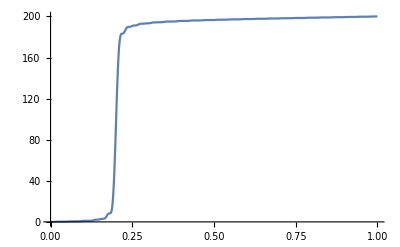

```mathematica
q1=ListPlot[aa1,Joined->True]
```

```mathematica
a2=Table[F[1,1,1/10,50,x],{x,0,1,0.001}]
```

{0.,0.015881,0.0310628,0.0449165,0.0569456,0.0668309,0.0744541,0.0798963,0.0834126,0.0853867,0.0862711,0.0865227,0.0865413,0.0866216,0.0869249,0.0874752,0.0881816,0.0888847,0.0894197,0.0896902,0.0897393,0.0898082,0.0903717,0.0921423,0.0960378,0.103113,0.114459,0.131081,0.153766,0.182955,0.218639,0.260293,0.306858,0.356782,0.408122,0.458695,0.506272,0.548801,0.584624,0.612676,0.632629,0.64498,0.651041,0.652848,0.652982,0.654307,0.65967,0.671564,0.691819,0.721342,0.759941,0.806274,0.857936,0.911683,0.9638,1.01057,1.04881,1.07643,1.09294,1.09987,1.10097,1.10224,1.1117,1.13891,1.19423,1.28786,1.4288,1.62377,1.87611,2.18497,2.54478,2.94505,3.37072,3.80306,4.221,4.60309,4.92978,5.18599,5.36386,5.46532,5.50441,5.5091,5.52235,5.60233,5.82161,6.26533,7.0283,8.21113,9.91562,12.2395,15.2711,19.0835,23.7298,29.2386,35.6107,42.8165,50.7961,59.4595,68.6894,78.3451,88.2679,98.2869,108.227,117.914,127.186,135.894,143.916,151.153,157.538,163.037,167.645,171.391,174.329,176.537,178.11,179.155,179.784,180.11,180.238,180.264,180.268,180.314,180.447,180.695,181.067,181.556,182.147,182.812,183.519,184.234,184.924,185.562,186.124,186.596,186.971,187.25,187.441,187.557,187.616,187.637,187.64,187.642,187.66,187.702,187.777,187.885,188.024,188.187,188.366,188.55,188.728,188.891,189.031,189.144,189.227,189.281,189.311,189.323,189.325,189.326,189.335,189.361,189.408,189.482,189.585,189.714,189.867,190.038,190.221,190.406,190.587,190.756,190.907,191.036,191.139,191.217,191.271,191.304,191.321,191.327,191.328,191.329,191.334,191.347,191.37,191.403,191.445,191.494,191.548,191.603,191.655,191.702,191.741,191.77,191.79,191.801,191.805,191.806,191.807,191.811,191.822,191.844,191.878,191.926,191.989,192.064,192.151,192.245,192.344,192.443,192.538,192.627,192.705,192.771,192.824,192.864,192.891,192.908,192.916,192.92,192.92,192.92,192.923,192.929,192.94,192.956,192.976,192.999,193.023,193.047,193.07,193.089,193.104,193.114,193.12,193.123,193.123,193.123,193.126,193.132,193.144,193.164,193.193,193.231,193.278,193.333,193.394,193.46,193.527,193.593,193.656,193.714,193.765,193.807,193.841,193.866,193.883,193.893,193.898,193.9,193.901,193.901,193.902,193.906,193.912,193.921,193.932,193.945,193.958,193.97,193.981,193.99,193.997,194.001,194.002,194.003,194.003,194.004,194.008,194.016,194.029,194.048,194.074,194.106,194.145,194.189,194.237,194.287,194.338,194.388,194.434,194.476,194.513,194.543,194.567,194.584,194.596,194.603,194.607,194.608,194.608,194.608,194.609,194.612,194.616,194.621,194.628,194.635,194.643,194.65,194.656,194.66,194.663,194.664,194.664,194.664,194.665,194.667,194.673,194.682,194.695,194.714,194.738,194.767,194.8,194.837,194.877,194.918,194.959,194.999,195.035,195.068,195.096,195.119,195.137,195.15,195.159,195.164,195.166,195.167,195.167,195.167,195.168,195.17,195.172,195.176,195.18,195.185,195.189,195.193,195.196,195.198,195.199,195.2,195.2,195.2,195.202,195.205,195.211,195.221,195.235,195.253,195.276,195.302,195.332,195.365,195.399,195.434,195.469,195.501,195.531,195.557,195.58,195.598,195.612,195.622,195.629,195.633,195.635,195.635,195.635,195.636,195.636,195.637,195.639,195.641,195.644,195.647,195.65,195.652,195.653,195.654,195.654,195.654,195.655,195.656,195.658,195.663,195.67,195.681,195.695,195.713,195.734,195.759,195.786,195.815,195.846,195.876,195.906,195.933,195.958,195.98,195.999,196.014,196.025,196.033,196.038,196.041,196.043,196.043,196.043,196.043,196.044,196.045,196.046,196.048,196.049,196.051,196.053,196.054,196.055,196.055,196.055,196.055,196.056,196.057,196.061,196.066,196.074,196.086,196.1,196.118,196.138,196.161,196.187,196.213,196.241,196.267,196.293,196.317,196.339,196.357,196.373,196.385,196.394,196.401,196.405,196.408,196.409,196.409,196.409,196.409,196.41,196.41,196.411,196.412,196.414,196.415,196.415,196.416,196.416,196.416,196.416,196.417,196.418,196.42,196.425,196.431,196.44,196.452,196.466,196.483,196.503,196.525,196.549,196.574,196.598,196.623,196.646,196.667,196.685,196.701,196.715,196.725,196.733,196.738,196.742,196.744,196.745,196.745,196.745,196.745,196.745,196.746,196.746,196.747,196.748,196.748,196.749,196.749,196.749,196.749,196.749,196.75,196.752,196.755,196.76,196.767,196.777,196.789,196.804,196.821,196.84,196.861,196.884,196.906,196.929,196.951,196.972,196.99,197.007,197.021,197.032,197.041,197.048,197.052,197.055,197.057,197.057,197.058,197.058,197.058,197.058,197.058,197.059,197.059,197.06,197.06,197.06,197.06,197.06,197.06,197.061,197.062,197.065,197.068,197.074,197.082,197.092,197.105,197.119,197.137,197.155,197.176,197.197,197.218,197.239,197.259,197.278,197.295,197.309,197.322,197.331,197.339,197.345,197.349,197.351,197.352,197.353,197.353,197.353,197.353,197.353,197.353,197.354,197.354,197.354,197.354,197.354,197.354,197.355,197.355,197.356,197.358,197.361,197.365,197.372,197.38,197.391,197.404,197.419,197.436,197.454,197.473,197.494,197.514,197.533,197.552,197.569,197.584,197.597,197.608,197.616,197.623,197.628,197.631,197.633,197.634,197.635,197.635,197.635,197.635,197.635,197.635,197.635,197.635,197.636,197.636,197.636,197.636,197.636,197.637,197.638,197.64,197.644,197.649,197.656,197.665,197.676,197.69,197.705,197.721,197.739,197.758,197.778,197.797,197.815,197.832,197.848,197.861,197.873,197.883,197.89,197.896,197.9,197.903,197.904,197.905,197.906,197.906,197.906,197.906,197.906,197.906,197.906,197.906,197.906,197.906,197.906,197.907,197.907,197.908,197.91,197.913,197.917,197.923,197.93,197.94,197.952,197.965,197.98,197.997,198.015,198.033,198.051,198.069,198.087,198.102,198.117,198.129,198.14,198.148,198.155,198.16,198.164,198.166,198.167,198.168,198.168,198.168,198.169,198.169,198.169,198.169,198.169,198.169,198.169,198.169,198.169,198.169,198.17,198.171,198.173,198.177,198.182,198.188,198.196,198.207,198.219,198.232,198.248,198.264,198.282,198.299,198.317,198.334,198.35,198.365,198.378,198.39,198.399,198.407,198.413,198.417,198.42,198.422,198.423,198.424,198.424,198.424,198.424,198.424,198.424,198.424,198.424,198.424,198.424,198.424,198.425,198.425,198.426,198.428,198.431,198.435,198.44,198.447,198.456,198.467,198.479,198.493,198.509,198.525,198.542,198.559,198.576,198.593,198.608,198.622,198.634,198.644,198.653,198.66,198.665,198.669,198.671,198.673,198.674,198.675,198.675,198.675,198.675,198.675,198.675,198.675,198.675,198.675,198.675,198.675,198.675,198.676,198.677,198.679,198.683,198.687,198.693,198.701,198.71,198.722,198.734,198.749,198.764,198.781,198.797,198.814,198.831,198.846,198.861,198.873,198.885,198.894,198.902,198.908,198.913,198.916,198.918,198.92,198.92,198.921,198.921,198.921,198.921,198.921,198.921,198.921,198.921,198.921,198.921,198.921,198.922,198.923,198.924,198.927,198.931,198.936,198.942,198.951,198.961,198.973,198.986,199.,199.016,199.032,199.049,199.065,199.081,199.096,199.109,199.121,199.132,199.14,199.148,199.153,199.157,199.16,199.162,199.163,199.163,199.164,199.164,199.164,199.164,199.164,199.164,199.164,199.164,199.164,199.164,199.164,199.165,199.166,199.168,199.171,199.176,199.181,199.189,199.198,199.208,199.22,199.234,199.249,199.265,199.281,199.297,199.313,199.328,199.342,199.355,199.366,199.376,199.384,199.39,199.395,199.399,199.401,199.403,199.404,199.404,199.404,199.404,199.404,199.404,199.404,199.404,199.404,199.404,199.405,199.405,199.405,199.406,199.408,199.41,199.414,199.418,199.425,199.433,199.442,199.453,199.466,199.48,199.495,199.511,199.527,199.543,199.559,199.573,199.587,199.599,199.609,199.618,199.626,199.631,199.636,199.639,199.641,199.642,199.643,199.643,199.643,199.643,199.643,199.643,199.643,199.643,199.643,199.643,199.644,199.644,199.645,199.646,199.648,199.65,199.654,199.66,199.667,199.675,199.685,199.697,199.71,199.725,199.74,199.756,199.772,199.788,199.803,199.817,199.83,199.841,199.851,199.859,199.866,199.871,199.875,199.877,199.879,199.88,199.881,199.881,199.881,199.881,199.881,199.881,199.881,199.881,199.881,199.881,199.882,199.882,199.883,199.884,199.887,199.89,199.894,199.9,199.908,199.917,199.928,199.94,199.954,199.969,199.984,200.}

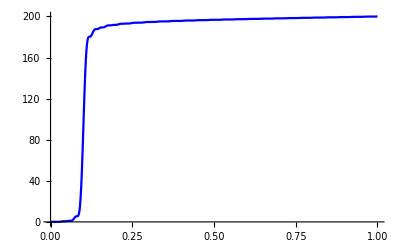

```mathematica
aa2=Transpose[{b,a2}];
q2=ListPlot[aa2,Joined->True,PlotStyle->Blue]
```

```mathematica
a3=Table[F[1,1,1/25,50,x],{x,0,1,0.001}]
```

{0.,4.4695×10^-6,0.00014104,0.0010463,0.00426655,0.0124782,0.0294637,0.0598181,0.108402,0.179598,0.276467,0.399915,0.548029,0.715697,0.894649,1.07401,1.24138,1.38451,1.49338,1.5627,1.59446,1.60054,1.60492,1.64536,1.77424,2.05849,2.57833,3.42485,4.6965,6.49449,8.91751,12.0559,15.9855,20.7624,26.4174,32.952,40.3362,48.5072,57.3697,66.7993,76.6459,86.7402,96.9002,106.939,116.674,125.934,134.567,142.446,149.477,155.597,160.782,165.041,168.416,170.98,172.827,174.069,174.827,175.227,175.389,175.424,175.428,175.479,175.632,175.922,176.365,176.955,177.673,178.487,179.359,180.247,181.109,181.91,182.62,183.219,183.698,184.055,184.301,184.451,184.528,184.556,184.559,184.563,184.586,184.643,184.743,184.889,185.077,185.299,185.545,185.799,186.047,186.277,186.478,186.641,186.764,186.847,186.895,186.916,186.921,186.922,186.93,186.957,187.012,187.101,187.227,187.388,187.582,187.801,188.037,188.279,188.516,188.739,188.939,189.111,189.249,189.354,189.427,189.472,189.496,189.504,189.505,189.506,189.514,189.532,189.564,189.611,189.671,189.743,189.821,189.902,189.98,190.051,190.112,190.159,190.192,190.213,190.222,190.225,190.225,190.228,190.238,190.261,190.3,190.356,190.431,190.523,190.631,190.75,190.876,191.003,191.127,191.243,191.346,191.434,191.505,191.558,191.595,191.617,191.629,191.633,191.634,191.634,191.638,191.647,191.663,191.685,191.714,191.748,191.784,191.821,191.856,191.887,191.911,191.93,191.941,191.947,191.949,191.949,191.95,191.956,191.967,191.988,192.02,192.063,192.118,192.184,192.258,192.338,192.422,192.506,192.586,192.66,192.725,192.781,192.825,192.858,192.881,192.894,192.902,192.904,192.904,192.905,192.907,192.912,192.921,192.934,192.95,192.969,192.988,193.008,193.026,193.041,193.052,193.06,193.064,193.065,193.066,193.066,193.069,193.076,193.088,193.108,193.136,193.172,193.216,193.268,193.325,193.385,193.447,193.508,193.566,193.619,193.665,193.704,193.735,193.757,193.773,193.782,193.787,193.789,193.789,193.789,193.791,193.794,193.8,193.808,193.818,193.829,193.84,193.851,193.861,193.869,193.874,193.877,193.878,193.879,193.879,193.88,193.884,193.893,193.906,193.925,193.95,193.982,194.02,194.062,194.109,194.157,194.206,194.254,194.299,194.339,194.374,194.403,194.425,194.442,194.453,194.46,194.464,194.465,194.465,194.465,194.466,194.468,194.472,194.477,194.484,194.491,194.498,194.504,194.51,194.514,194.516,194.517,194.517,194.517,194.518,194.521,194.526,194.535,194.549,194.567,194.591,194.62,194.653,194.69,194.729,194.77,194.81,194.849,194.885,194.917,194.944,194.967,194.985,194.997,195.006,195.011,195.014,195.014,195.015,195.015,195.015,195.017,195.02,195.023,195.027,195.032,195.036,195.04,195.043,195.045,195.046,195.046,195.046,195.046,195.048,195.052,195.058,195.068,195.082,195.1,195.122,195.149,195.179,195.212,195.246,195.281,195.315,195.347,195.377,195.404,195.426,195.444,195.458,195.468,195.475,195.479,195.481,195.482,195.482,195.482,195.482,195.483,195.485,195.488,195.491,195.493,195.496,195.498,195.5,195.501,195.501,195.501,195.501,195.502,195.505,195.509,195.516,195.527,195.541,195.559,195.581,195.605,195.633,195.662,195.693,195.723,195.753,195.781,195.806,195.828,195.847,195.862,195.873,195.881,195.887,195.89,195.892,195.892,195.892,195.892,195.893,195.893,195.895,195.896,195.898,195.9,195.902,195.903,195.904,195.904,195.904,195.904,195.905,195.906,195.91,195.915,195.923,195.934,195.949,195.966,195.987,196.01,196.036,196.063,196.09,196.117,196.143,196.168,196.19,196.209,196.224,196.237,196.246,196.253,196.258,196.26,196.261,196.262,196.262,196.262,196.262,196.263,196.264,196.265,196.266,196.267,196.268,196.269,196.269,196.269,196.269,196.269,196.271,196.273,196.277,196.283,196.292,196.304,196.318,196.336,196.356,196.378,196.402,196.427,196.452,196.476,196.499,196.521,196.54,196.556,196.57,196.581,196.589,196.594,196.598,196.6,196.601,196.601,196.601,196.601,196.601,196.602,196.603,196.603,196.604,196.605,196.605,196.606,196.606,196.606,196.606,196.607,196.608,196.611,196.616,196.623,196.633,196.645,196.659,196.677,196.696,196.717,196.74,196.763,196.786,196.808,196.829,196.848,196.865,196.88,196.891,196.901,196.907,196.912,196.915,196.917,196.917,196.918,196.918,196.918,196.918,196.918,196.919,196.919,196.92,196.92,196.92,196.92,196.92,196.921,196.921,196.922,196.925,196.928,196.934,196.941,196.951,196.964,196.979,196.996,197.015,197.035,197.057,197.078,197.1,197.12,197.139,197.156,197.171,197.184,197.194,197.202,197.208,197.212,197.214,197.216,197.216,197.217,197.217,197.217,197.217,197.217,197.217,197.218,197.218,197.218,197.218,197.218,197.218,197.219,197.219,197.221,197.224,197.228,197.235,197.243,197.253,197.266,197.281,197.298,197.317,197.336,197.357,197.377,197.397,197.416,197.433,197.449,197.462,197.473,197.482,197.489,197.494,197.498,197.5,197.501,197.501,197.502,197.502,197.502,197.502,197.502,197.502,197.502,197.502,197.503,197.503,197.503,197.503,197.503,197.505,197.507,197.51,197.515,197.522,197.531,197.542,197.555,197.57,197.587,197.605,197.624,197.644,197.663,197.682,197.699,197.715,197.729,197.741,197.751,197.759,197.765,197.769,197.772,197.774,197.775,197.775,197.776,197.776,197.776,197.776,197.776,197.776,197.776,197.776,197.776,197.776,197.776,197.777,197.777,197.779,197.782,197.786,197.791,197.799,197.808,197.82,197.833,197.849,197.865,197.883,197.901,197.92,197.938,197.956,197.972,197.987,198.,198.011,198.02,198.027,198.032,198.035,198.038,198.039,198.04,198.04,198.041,198.041,198.041,198.041,198.041,198.041,198.041,198.041,198.041,198.041,198.041,198.042,198.043,198.045,198.048,198.053,198.059,198.067,198.077,198.089,198.103,198.118,198.135,198.152,198.17,198.188,198.206,198.222,198.237,198.251,198.263,198.272,198.28,198.287,198.291,198.294,198.296,198.298,198.298,198.299,198.299,198.299,198.299,198.299,198.299,198.299,198.299,198.299,198.299,198.299,198.299,198.3,198.302,198.304,198.308,198.313,198.32,198.329,198.339,198.352,198.366,198.381,198.398,198.415,198.432,198.449,198.466,198.482,198.496,198.508,198.519,198.528,198.535,198.541,198.545,198.547,198.549,198.55,198.551,198.551,198.551,198.551,198.551,198.551,198.551,198.551,198.551,198.551,198.551,198.551,198.552,198.553,198.555,198.558,198.562,198.568,198.576,198.585,198.596,198.609,198.623,198.638,198.655,198.672,198.689,198.705,198.721,198.736,198.749,198.761,198.771,198.779,198.785,198.79,198.793,198.796,198.797,198.798,198.798,198.799,198.799,198.799,198.799,198.799,198.799,198.799,198.799,198.799,198.799,198.799,198.8,198.802,198.804,198.808,198.813,198.819,198.827,198.837,198.848,198.861,198.876,198.891,198.908,198.924,198.941,198.957,198.972,198.986,198.998,199.009,199.018,199.025,199.031,199.035,199.038,199.04,199.042,199.042,199.043,199.043,199.043,199.043,199.043,199.043,199.043,199.043,199.043,199.043,199.043,199.044,199.045,199.047,199.05,199.054,199.059,199.066,199.075,199.085,199.097,199.111,199.125,199.141,199.157,199.174,199.19,199.205,199.22,199.233,199.244,199.254,199.263,199.269,199.274,199.278,199.281,199.282,199.283,199.284,199.284,199.284,199.284,199.284,199.284,199.284,199.284,199.284,199.284,199.285,199.285,199.286,199.287,199.29,199.293,199.297,199.303,199.311,199.32,199.331,199.344,199.358,199.372,199.388,199.404,199.42,199.436,199.451,199.465,199.477,199.488,199.497,199.505,199.511,199.516,199.519,199.521,199.522,199.523,199.524,199.524,199.524,199.524,199.524,199.524,199.524,199.524,199.524,199.524,199.524,199.525,199.526,199.528,199.53,199.534,199.539,199.546,199.554,199.564,199.575,199.588,199.603,199.618,199.634,199.65,199.666,199.681,199.695,199.708,199.72,199.73,199.739,199.746,199.751,199.755,199.758,199.76,199.761,199.762,199.762,199.762,199.762,199.762,199.762,199.762,199.762,199.762,199.762,199.763,199.763,199.764,199.765,199.767,199.77,199.774,199.78,199.787,199.796,199.807,199.819,199.832,199.847,199.862,199.878,199.894,199.91,199.925,199.938,199.951,199.962,199.972,199.98,199.986,199.991,199.994,199.997,199.998,199.999,200.,200.,200.,200.,200.,200.}

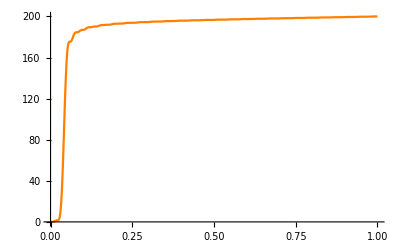

```mathematica
aa3=Transpose[{b,a3}];
q3=ListPlot[aa3,Joined->True,PlotStyle->Orange]
```

```mathematica
a4=Table[F[1,1,1/2,50,x],{x,0,1,0.001}]
```

{0.,0.0159318,0.0314595,0.0462047,0.0598379,0.0720975,0.0828037,0.0918646,0.0992762,0.105114,0.109521,0.112689,0.114839,0.116198,0.116985,0.117391,0.117568,0.117629,0.117643,0.117644,0.117644,0.117644,0.117653,0.117698,0.117841,0.118183,0.118868,0.120081,0.122036,0.124961,0.129084,0.134607,0.141686,0.150417,0.160816,0.172811,0.186242,0.200864,0.216359,0.232354,0.248444,0.264219,0.279286,0.293299,0.305975,0.317113,0.326598,0.334408,0.340601,0.345311,0.348721,0.351054,0.352541,0.353409,0.353859,0.354056,0.354122,0.354136,0.354136,0.354137,0.354138,0.35414,0.354163,0.35426,0.354522,0.355086,0.356132,0.357875,0.36055,0.364394,0.369625,0.37642,0.384897,0.395095,0.406963,0.42036,0.435052,0.450729,0.467016,0.4835,0.499755,0.515368,0.529967,0.543242,0.554965,0.564997,0.573295,0.579904,0.584949,0.588613,0.591123,0.592722,0.593649,0.594122,0.59432,0.594379,0.594387,0.594389,0.594397,0.594405,0.594407,0.594412,0.594459,0.594631,0.595057,0.595916,0.597425,0.599832,0.60339,0.60834,0.614886,0.623173,0.633268,0.645145,0.65868,0.67365,0.689746,0.706585,0.723738,0.740752,0.757183,0.772625,0.786731,0.79924,0.809984,0.818896,0.82601,0.831443,0.835385,0.838073,0.839769,0.840732,0.841204,0.841385,0.841427,0.841429,0.841442,0.841474,0.841514,0.84154,0.841545,0.841554,0.841637,0.841914,0.842565,0.843814,0.845926,0.849179,0.853846,0.860166,0.868321,0.878413,0.890446,0.904314,0.919806,0.936608,0.954322,0.972491,0.990624,1.00823,1.02486,1.04011,1.05369,1.06537,1.07508,1.08283,1.08874,1.093,1.09587,1.09765,1.09863,1.09907,1.09922,1.09924,1.09924,1.0993,1.0994,1.09952,1.09962,1.09968,1.09969,1.09971,1.09984,1.10027,1.10123,1.10301,1.10593,1.11029,1.1164,1.12448,1.13468,1.14704,1.16149,1.17782,1.1957,1.21473,1.23439,1.25414,1.27344,1.29174,1.3086,1.32364,1.33661,1.34738,1.35596,1.36247,1.36711,1.3702,1.37205,1.37301,1.3734,1.37349,1.3735,1.37355,1.37371,1.37397,1.37429,1.37459,1.37481,1.37491,1.37493,1.37496,1.37517,1.37582,1.37722,1.37975,1.38378,1.38968,1.39774,1.40819,1.42111,1.43647,1.45408,1.4736,1.49457,1.51643,1.53855,1.56029,1.58102,1.60018,1.61731,1.63209,1.64436,1.65408,1.66139,1.66654,1.66987,1.67179,1.6727,1.67301,1.67305,1.67308,1.67326,1.67368,1.67429,1.67503,1.67578,1.6764,1.67683,1.67702,1.67705,1.67709,1.67742,1.6784,1.68047,1.68411,1.68978,1.6979,1.70878,1.72261,1.73939,1.75896,1.78097,1.8049,1.8301,1.85581,1.88124,1.90562,1.92824,1.9485,1.96599,1.98045,1.99185,2.00032,2.00616,2.00981,2.01178,2.0126,2.0128,2.01281,2.01299,2.01353,2.01453,2.01593,2.01759,2.01932,2.02089,2.02212,2.0229,2.02325,2.0233,2.02337,2.02389,2.02541,2.02856,2.03397,2.04224,2.05386,2.06914,2.08819,2.1109,2.13689,2.16556,2.19611,2.22759,2.25898,2.28924,2.31743,2.34274,2.36456,2.38254,2.39657,2.40684,2.41373,2.41783,2.41985,2.42053,2.42061,2.42073,2.42136,2.42281,2.42518,2.42837,2.43215,2.43614,2.43995,2.4432,2.44562,2.4471,2.44773,2.44783,2.44794,2.44882,2.45132,2.45641,2.46498,2.47786,2.49562,2.51858,2.54671,2.57964,2.61663,2.65663,2.69834,2.74033,2.78111,2.81929,2.85364,2.88323,2.90747,2.9262,2.93961,2.94829,2.95312,2.95519,2.95567,2.95572,2.95636,2.95838,2.96226,2.96816,2.9759,2.98499,2.99474,3.00437,3.01307,3.02018,3.02529,3.02832,3.02958,3.02978,3.03,3.03163,3.03624,3.04543,3.06069,3.08324,3.11387,3.15283,3.1998,3.25381,3.31337,3.37646,3.44079,3.5039,3.56338,3.61709,3.66336,3.70106,3.72979,3.74985,3.76223,3.76848,3.77062,3.77084,3.77139,3.77425,3.78101,3.79268,3.80956,3.83129,3.85683,3.88463,3.91282,3.93942,3.96263,3.98107,3.99402,4.00153,4.0046,4.00507,4.00559,4.00939,4.01999,4.04091,4.07526,4.12544,4.19282,4.27753,4.37832,4.4926,4.61657,4.74548,4.87403,4.99677,5.10863,5.20539,5.28408,5.34331,5.38349,5.40678,5.41701,5.41931,5.4197,5.42444,5.4395,5.46986,5.519,5.58846,5.6776,5.78359,5.90158,6.02518,6.1471,6.25992,6.35705,6.43352,6.4869,6.51783,6.53044,6.53239,6.53455,6.55036,6.59482,6.68317,6.82951,7.04526,7.3377,7.70882,8.15446,8.66396,9.22041,9.80153,10.3811,10.9314,11.4251,11.839,12.1568,12.3719,12.4904,12.5333,12.5376,12.5571,12.6619,12.936,13.4755,14.3837,15.7674,17.7307,20.3698,23.7672,27.9865,33.0674,39.0222,45.8334,53.4525,61.8007,70.7707,80.2307,90.029,100.,109.971,119.769,129.229,138.199,146.547,154.167,160.978,166.933,172.014,176.233,179.63,182.269,184.233,185.616,186.525,187.064,187.338,187.443,187.462,187.467,187.51,187.628,187.843,188.161,188.575,189.069,189.619,190.198,190.78,191.336,191.846,192.291,192.662,192.955,193.17,193.317,193.405,193.45,193.465,193.468,193.47,193.482,193.513,193.566,193.643,193.74,193.853,193.975,194.098,194.216,194.322,194.412,194.481,194.53,194.561,194.576,194.58,194.581,194.583,194.593,194.617,194.657,194.716,194.795,194.891,195.003,195.126,195.255,195.383,195.507,195.622,195.722,195.807,195.875,195.925,195.959,195.98,195.991,195.994,195.995,195.995,195.998,196.006,196.019,196.037,196.061,196.087,196.115,196.143,196.169,196.19,196.207,196.219,196.226,196.229,196.229,196.229,196.232,196.238,196.25,196.27,196.299,196.337,196.383,196.437,196.496,196.559,196.624,196.687,196.746,196.8,196.847,196.886,196.917,196.939,196.955,196.964,196.968,196.97,196.97,196.97,196.972,196.975,196.98,196.987,196.996,197.005,197.015,197.024,197.032,197.038,197.042,197.044,197.044,197.044,197.045,197.047,197.052,197.06,197.074,197.093,197.117,197.146,197.181,197.219,197.26,197.302,197.343,197.383,197.42,197.453,197.481,197.504,197.522,197.535,197.544,197.549,197.551,197.552,197.552,197.552,197.553,197.554,197.557,197.56,197.564,197.568,197.572,197.575,197.577,197.579,197.579,197.579,197.579,197.58,197.582,197.586,197.593,197.603,197.617,197.635,197.657,197.683,197.711,197.741,197.772,197.804,197.834,197.863,197.889,197.912,197.931,197.946,197.958,197.966,197.971,197.975,197.976,197.977,197.977,197.977,197.977,197.978,197.979,197.981,197.982,197.984,197.985,197.986,197.987,197.987,197.987,197.987,197.988,197.99,197.994,198.,198.008,198.02,198.034,198.051,198.072,198.094,198.119,198.144,198.17,198.195,198.219,198.241,198.261,198.277,198.291,198.302,198.31,198.316,198.32,198.322,198.323,198.323,198.323,198.323,198.323,198.324,198.324,198.325,198.326,198.326,198.327,198.327,198.327,198.327,198.327,198.328,198.33,198.333,198.339,198.346,198.356,198.368,198.383,198.4,198.419,198.44,198.461,198.484,198.505,198.526,198.546,198.564,198.579,198.592,198.602,198.61,198.616,198.62,198.623,198.624,198.625,198.625,198.625,198.625,198.625,198.625,198.626,198.626,198.626,198.626,198.627,198.627,198.627,198.627,198.628,198.63,198.633,198.638,198.644,198.653,198.663,198.676,198.691,198.708,198.727,198.746,198.766,198.785,198.804,198.822,198.839,198.853,198.865,198.876,198.884,198.89,198.894,198.897,198.899,198.9,198.9,198.9,198.9,198.9,198.9,198.9,198.901,198.901,198.901,198.901,198.901,198.901,198.901,198.902,198.904,198.907,198.911,198.917,198.925,198.935,198.946,198.96,198.975,198.992,199.009,199.028,199.046,199.063,199.08,199.096,199.11,199.122,199.132,199.14,199.146,199.151,199.154,199.156,199.157,199.158,199.158,199.158,199.158,199.158,199.158,199.159,199.159,199.159,199.159,199.159,199.159,199.159,199.16,199.162,199.165,199.169,199.174,199.181,199.19,199.201,199.213,199.227,199.243,199.259,199.276,199.293,199.31,199.326,199.341,199.355,199.367,199.377,199.385,199.392,199.397,199.4,199.403,199.404,199.405,199.405,199.406,199.406,199.406,199.406,199.406,199.406,199.406,199.406,199.406,199.406,199.406,199.407,199.409,199.411,199.415,199.42,199.427,199.435,199.445,199.457,199.47,199.485,199.5,199.516,199.533,199.549,199.565,199.58,199.593,199.605,199.615,199.624,199.63,199.636,199.639,199.642,199.644,199.645,199.645,199.646,199.646,199.646,199.646,199.646,199.646,199.646,199.646,199.646,199.646,199.647,199.647,199.649,199.651,199.655,199.659,199.666,199.673,199.683,199.694,199.707,199.721,199.736,199.752,199.768,199.784,199.799,199.814,199.827,199.839,199.85,199.858,199.865,199.871,199.875,199.878,199.88,199.881,199.882,199.882,199.882,199.882,199.882,199.882,199.882,199.882,199.882,199.882,199.883,199.883,199.884,199.885,199.887,199.89,199.895,199.901,199.908,199.917,199.928,199.94,199.954,199.969,199.984,200.}

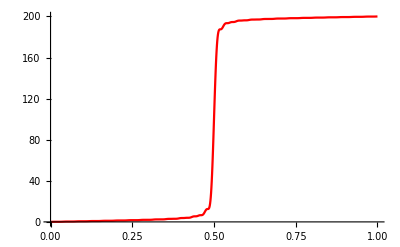

```mathematica
aa4=Transpose[{b,a4}];
q4=ListPlot[aa4,Joined->True,PlotStyle->Red]
```

```mathematica
a5=Table[F[1,1,0.4,50,x],{x,0,1,0.001}]
```

{0.,1.35845×10^-7,4.30683×10^-6,0.0000322021,0.000132786,0.000394076,0.000947676,0.00196726,0.0036608,0.00625717,0.00998816,0.0150678,0.0216706,0.0299119,0.0398309,0.0513802,0.0644206,0.0787249,0.0939879,0.109844,0.125889,0.141706,0.156893,0.171087,0.18399,0.195379,0.205124,0.213184,0.219608,0.224516,0.228091,0.23055,0.23213,0.23306,0.233549,0.233767,0.233842,0.233858,0.233859,0.23386,0.23386,0.233862,0.233885,0.23398,0.234239,0.234802,0.23585,0.237602,0.240298,0.244178,0.249467,0.256342,0.264923,0.275245,0.287255,0.300802,0.315644,0.331456,0.347854,0.364411,0.380692,0.396277,0.410791,0.423925,0.435458,0.445259,0.453299,0.459638,0.464415,0.46783,0.470119,0.471536,0.472324,0.4727,0.472841,0.472873,0.472875,0.472881,0.472897,0.47291,0.472913,0.47292,0.472979,0.473188,0.473697,0.474704,0.47645,0.479199,0.483218,0.488754,0.496006,0.505106,0.516094,0.528911,0.543391,0.559267,0.57618,0.593705,0.611375,0.628708,0.645248,0.660583,0.674384,0.686413,0.69654,0.704746,0.711111,0.715803,0.719056,0.721144,0.722351,0.722952,0.723185,0.723238,0.723241,0.723265,0.72333,0.723421,0.723504,0.723551,0.723561,0.723575,0.723695,0.724085,0.724973,0.726634,0.729377,0.733516,0.739345,0.747104,0.756952,0.768948,0.783028,0.799008,0.816581,0.835336,0.854781,0.874373,0.893558,0.911805,0.928644,0.943696,0.956698,0.967513,0.976131,0.982668,0.987337,0.99043,0.99228,0.993233,0.993615,0.993703,0.993708,0.993767,0.99394,0.99422,0.994557,0.994875,0.995108,0.995222,0.995243,0.99527,0.99549,0.99617,0.997646,1.0003,1.00453,1.01071,1.01916,1.03009,1.0436,1.05962,1.07795,1.09823,1.11996,1.14254,1.1653,1.18757,1.20869,1.22809,1.2453,1.26001,1.27207,1.28147,1.2884,1.29313,1.29607,1.29764,1.2983,1.29846,1.29847,1.29858,1.29895,1.2996,1.3005,1.30151,1.30249,1.3033,1.30383,1.30407,1.30411,1.30416,1.30455,1.30572,1.30817,1.31244,1.31907,1.32849,1.34104,1.35688,1.37599,1.39813,1.42285,1.44951,1.47735,1.50548,1.53302,1.55908,1.5829,1.60388,1.62159,1.63585,1.6467,1.65438,1.65934,1.66212,1.66336,1.6637,1.66372,1.66391,1.66459,1.66593,1.66794,1.67046,1.67326,1.67603,1.67845,1.68029,1.68143,1.68193,1.68201,1.6821,1.68282,1.68489,1.68912,1.69633,1.70724,1.72241,1.74218,1.7666,1.79541,1.82802,1.86358,1.90098,1.93897,1.97624,2.01151,2.04363,2.0717,2.0951,2.11357,2.12719,2.13637,2.14183,2.14447,2.14531,2.14539,2.14564,2.14682,2.14944,2.15372,2.15957,2.16666,2.17444,2.18225,2.1894,2.19532,2.19962,2.20219,2.20326,2.20343,2.20362,2.20504,2.20908,2.21717,2.23067,2.25072,2.27808,2.31305,2.3554,2.40434,2.45857,2.51631,2.57551,2.63392,2.68933,2.73974,2.78353,2.8196,2.84745,2.86726,2.87982,2.88648,2.889,2.88939,2.88967,2.89171,2.89702,2.90659,2.92081,2.93943,2.9616,2.98596,3.01085,3.03449,3.05524,3.07181,3.08348,3.09029,3.09307,3.0935,3.09398,3.09747,3.10723,3.12653,3.15832,3.20488,3.26756,3.34656,3.4408,3.54793,3.66445,3.78596,3.90748,4.02388,4.13035,4.22282,4.29839,4.35564,4.39481,4.41784,4.42822,4.43074,4.43104,4.43506,4.44847,4.47607,4.52128,4.58566,4.66875,4.76797,4.87882,4.99529,5.11047,5.21732,5.3095,5.38223,5.43309,5.46261,5.47466,5.47652,5.4786,5.49379,5.53655,5.62167,5.76284,5.97124,6.2541,6.61353,7.0457,7.54044,8.08147,8.64721,9.21226,9.74936,10.232,10.6373,10.949,11.1604,11.2772,11.3197,11.324,11.3429,11.445,11.7136,12.2432,13.1365,14.4995,16.4361,19.0427,22.4023,26.5795,31.6153,37.5238,44.2892,51.8652,60.1748,69.1128,78.5486,88.3319,98.2978,108.274,118.087,127.571,136.573,144.96,152.622,159.479,165.48,170.606,174.867,178.302,180.973,182.963,184.367,185.29,185.84,186.119,186.227,186.247,186.251,186.294,186.415,186.633,186.957,187.38,187.884,188.447,189.041,189.638,190.209,190.733,191.192,191.575,191.877,192.1,192.251,192.343,192.389,192.405,192.407,192.409,192.422,192.455,192.511,192.591,192.693,192.811,192.94,193.07,193.195,193.308,193.403,193.478,193.531,193.564,193.58,193.586,193.586,193.589,193.599,193.622,193.663,193.724,193.806,193.907,194.024,194.153,194.288,194.424,194.555,194.676,194.783,194.874,194.945,194.999,195.036,195.058,195.07,195.074,195.074,195.075,195.078,195.087,195.101,195.121,195.147,195.176,195.207,195.239,195.267,195.292,195.312,195.325,195.334,195.337,195.338,195.338,195.34,195.346,195.358,195.379,195.408,195.447,195.496,195.553,195.616,195.683,195.752,195.821,195.885,195.944,195.995,196.038,196.071,196.096,196.113,196.124,196.129,196.13,196.131,196.131,196.132,196.136,196.142,196.15,196.16,196.172,196.183,196.194,196.204,196.211,196.217,196.22,196.221,196.221,196.221,196.223,196.227,196.235,196.249,196.267,196.292,196.323,196.36,196.4,196.444,196.49,196.536,196.58,196.621,196.657,196.689,196.715,196.735,196.749,196.759,196.765,196.768,196.769,196.769,196.769,196.77,196.772,196.775,196.779,196.784,196.789,196.794,196.798,196.802,196.804,196.805,196.806,196.806,196.806,196.807,196.811,196.817,196.827,196.841,196.859,196.882,196.908,196.938,196.971,197.005,197.04,197.074,197.106,197.135,197.161,197.183,197.201,197.214,197.224,197.23,197.234,197.236,197.237,197.237,197.237,197.237,197.238,197.24,197.242,197.244,197.247,197.249,197.251,197.252,197.252,197.253,197.253,197.253,197.254,197.257,197.262,197.27,197.281,197.295,197.313,197.334,197.358,197.384,197.411,197.44,197.468,197.495,197.52,197.543,197.562,197.578,197.591,197.601,197.608,197.613,197.615,197.617,197.617,197.617,197.617,197.617,197.618,197.619,197.62,197.621,197.622,197.623,197.624,197.624,197.624,197.624,197.625,197.626,197.628,197.633,197.639,197.648,197.66,197.674,197.692,197.711,197.733,197.757,197.781,197.805,197.829,197.851,197.872,197.89,197.906,197.918,197.928,197.936,197.941,197.944,197.946,197.947,197.947,197.947,197.947,197.947,197.948,197.948,197.949,197.949,197.95,197.95,197.95,197.95,197.95,197.951,197.952,197.954,197.958,197.963,197.971,197.98,197.993,198.008,198.025,198.044,198.064,198.086,198.107,198.129,198.149,198.168,198.186,198.201,198.213,198.223,198.231,198.237,198.241,198.243,198.245,198.245,198.246,198.246,198.246,198.246,198.246,198.246,198.246,198.247,198.247,198.247,198.247,198.247,198.247,198.248,198.25,198.253,198.258,198.264,198.273,198.284,198.297,198.312,198.329,198.347,198.366,198.386,198.406,198.425,198.443,198.46,198.474,198.487,198.497,198.506,198.512,198.516,198.519,198.521,198.522,198.523,198.523,198.523,198.523,198.523,198.523,198.523,198.523,198.523,198.524,198.524,198.524,198.524,198.525,198.526,198.529,198.533,198.539,198.546,198.556,198.567,198.581,198.596,198.613,198.63,198.649,198.667,198.685,198.703,198.719,198.733,198.746,198.757,198.766,198.772,198.777,198.781,198.783,198.785,198.785,198.786,198.786,198.786,198.786,198.786,198.786,198.786,198.786,198.786,198.786,198.786,198.787,198.787,198.789,198.791,198.794,198.799,198.806,198.814,198.825,198.837,198.851,198.866,198.883,198.9,198.917,198.935,198.952,198.968,198.982,198.995,199.006,199.015,199.022,199.028,199.032,199.035,199.037,199.038,199.038,199.039,199.039,199.039,199.039,199.039,199.039,199.039,199.039,199.039,199.039,199.039,199.04,199.041,199.043,199.046,199.05,199.056,199.064,199.073,199.084,199.097,199.111,199.127,199.143,199.16,199.177,199.193,199.209,199.223,199.236,199.248,199.257,199.265,199.272,199.276,199.279,199.282,199.283,199.284,199.284,199.284,199.284,199.284,199.284,199.284,199.284,199.284,199.285,199.285,199.285,199.285,199.286,199.288,199.291,199.294,199.3,199.306,199.315,199.325,199.337,199.35,199.365,199.38,199.397,199.413,199.429,199.445,199.46,199.473,199.485,199.495,199.503,199.51,199.515,199.519,199.522,199.523,199.524,199.525,199.525,199.525,199.525,199.525,199.525,199.525,199.525,199.525,199.526,199.526,199.526,199.527,199.528,199.531,199.534,199.539,199.545,199.552,199.562,199.573,199.585,199.599,199.614,199.63,199.646,199.662,199.678,199.693,199.706,199.718,199.729,199.738,199.745,199.751,199.756,199.759,199.761,199.762,199.763,199.763,199.763,199.763,199.763,199.763,199.763,199.763,199.763,199.763,199.764,199.764,199.765,199.766,199.768,199.771,199.775,199.78,199.787,199.796,199.806,199.818,199.831,199.846,199.861,199.877,199.893,199.909,199.924,199.938,199.95,199.962,199.971,199.979,199.986,199.99,199.994,199.997,199.998,199.999,200.,200.,200.,200.,200.,200.}

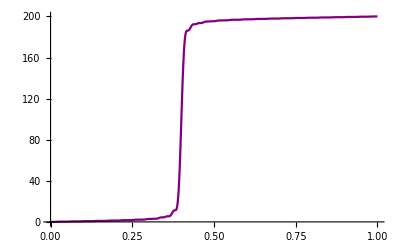

```mathematica
aa5=Transpose[{b,a5}];
q5=ListPlot[aa5,Joined->True,PlotStyle->Purple]
```

```mathematica
a6=Table[F[1,1,0.41,50,x],{x,0,1,0.001}]
```

{0.,0.000426263,0.000772253,0.000984668,0.00106105,0.00106776,0.00114987,0.00153162,0.00250698,0.00442102,0.00764354,0.0125375,0.019425,0.0285543,0.0400714,0.0539979,0.0702191,0.0884828,0.108409,0.12951,0.151224,0.172944,0.194065,0.214021,0.232322,0.248583,0.262549,0.2741,0.283254,0.290157,0.295056,0.298274,0.300178,0.301139,0.301509,0.301584,0.301592,0.30168,0.301915,0.302293,0.302757,0.303223,0.303606,0.303848,0.303941,0.30395,0.30402,0.304377,0.305323,0.30721,0.310421,0.315331,0.322276,0.331518,0.343213,0.357389,0.373936,0.392597,0.412987,0.434605,0.456869,0.479155,0.500834,0.521319,0.540098,0.556772,0.571071,0.582871,0.592193,0.599186,0.604112,0.607309,0.609164,0.610068,0.610389,0.61044,0.610458,0.610594,0.610914,0.611406,0.612002,0.612603,0.613108,0.613444,0.613594,0.613617,0.613659,0.613957,0.614828,0.616649,0.619831,0.624781,0.631865,0.641374,0.653484,0.668238,0.685527,0.705087,0.726509,0.749263,0.772727,0.79623,0.819099,0.840697,0.860474,0.877998,0.892979,0.905284,0.914939,0.922111,0.927088,0.930246,0.93201,0.93281,0.93305,0.933071,0.933129,0.933382,0.933892,0.934631,0.935508,0.936395,0.93716,0.937705,0.93799,0.938065,0.93808,0.938288,0.939036,0.940746,0.943878,0.948896,0.956222,0.966194,0.979027,0.994786,1.01336,1.03448,1.05769,1.08241,1.10794,1.13354,1.15845,1.18195,1.20343,1.22239,1.23853,1.25168,1.26189,1.26936,1.27442,1.27751,1.27914,1.27978,1.27992,1.27993,1.28012,1.28063,1.28154,1.28277,1.28421,1.28567,1.28695,1.28793,1.28852,1.28875,1.28878,1.28888,1.28945,1.291,1.29405,1.29918,1.30689,1.31761,1.33161,1.34901,1.3697,1.39336,1.4195,1.44744,1.47637,1.5054,1.53365,1.56027,1.58452,1.60584,1.62384,1.63836,1.64947,1.6574,1.6626,1.6656,1.66701,1.66746,1.6675,1.66761,1.66813,1.66923,1.67097,1.67323,1.67579,1.6784,1.68077,1.68266,1.68393,1.68458,1.68475,1.68478,1.68513,1.68644,1.68937,1.69467,1.703,1.71493,1.73086,1.75095,1.77512,1.80303,1.83406,1.86739,1.902,1.9368,1.97066,2.00252,2.03143,2.05669,2.07781,2.0946,2.10717,2.11587,2.12128,2.12414,2.12526,2.12547,2.12552,2.12603,2.12743,2.12992,2.13351,2.13799,2.14301,2.14812,2.15286,2.15681,2.15971,2.16145,2.16218,2.1623,2.16243,2.16339,2.16615,2.17173,2.1811,2.19511,2.21438,2.23921,2.26958,2.30507,2.3449,2.38795,2.43288,2.47817,2.52226,2.56365,2.60106,2.63347,2.66024,2.68113,2.69631,2.70635,2.71212,2.71475,2.71547,2.71552,2.71602,2.71789,2.72172,2.72778,2.73599,2.74594,2.75695,2.7682,2.77882,2.78801,2.79518,2.80004,2.80267,2.80357,2.80365,2.80416,2.80664,2.81272,2.82406,2.84211,2.868,2.90241,2.94544,2.99659,3.05475,3.11825,3.18498,3.25254,3.31843,3.38024,3.43584,3.48357,3.5224,3.55195,3.57259,3.58535,3.59183,3.59407,3.59432,3.59484,3.59768,3.60446,3.61628,3.63353,3.65591,3.68247,3.71174,3.74183,3.77076,3.79662,3.81789,3.8336,3.84355,3.84842,3.84973,3.84987,3.85183,3.85905,3.87506,3.90318,3.94616,4.00589,4.08312,4.17734,4.28672,4.40813,4.53741,4.66961,4.7994,4.9215,5.03118,5.12465,5.19945,5.25471,5.29128,5.31172,5.32009,5.32162,5.32227,5.32815,5.34496,5.37738,5.42862,5.49998,5.5907,5.69791,5.81687,5.94137,6.06435,6.17866,6.27784,6.35698,6.41347,6.44756,6.46277,6.46594,6.46701,6.47844,6.51433,6.5893,6.71722,6.90975,7.17507,7.5167,7.9326,8.41475,8.94915,9.51646,10.0931,10.653,11.17,11.6198,11.9835,12.2498,12.418,12.4998,12.5214,12.5241,12.5644,12.7128,13.0524,13.6752,14.6792,16.163,18.2219,20.9419,24.3952,28.6354,33.6936,39.5753,46.2584,53.6929,61.8012,70.4808,79.6069,89.0377,98.6194,108.192,117.597,126.68,135.304,143.344,150.703,157.305,163.105,168.083,172.248,175.634,178.296,180.306,181.752,182.728,183.332,183.661,183.804,183.842,183.845,183.866,183.945,184.108,184.364,184.714,185.145,185.64,186.174,186.724,187.264,187.772,188.23,188.624,188.947,189.199,189.381,189.502,189.573,189.607,189.618,189.619,189.622,189.636,189.666,189.717,189.789,189.878,189.981,190.092,190.204,190.31,190.406,190.487,190.55,190.595,190.623,190.638,190.642,190.643,190.645,190.653,190.672,190.706,190.756,190.825,190.91,191.009,191.12,191.237,191.356,191.472,191.581,191.68,191.764,191.834,191.888,191.927,191.953,191.968,191.974,191.977,191.977,191.978,191.981,191.989,192.001,192.018,192.039,192.062,192.086,192.109,192.13,192.147,192.161,192.169,192.174,192.176,192.177,192.177,192.179,192.186,192.197,192.216,192.242,192.276,192.318,192.366,192.42,192.476,192.534,192.592,192.646,192.696,192.74,192.778,192.808,192.83,192.847,192.857,192.863,192.865,192.866,192.866,192.867,192.868,192.871,192.876,192.882,192.889,192.897,192.904,192.91,192.916,192.92,192.922,192.923,192.923,192.923,192.924,192.927,192.932,192.941,192.955,192.973,192.996,193.023,193.054,193.089,193.125,193.163,193.2,193.235,193.268,193.298,193.323,193.344,193.36,193.373,193.381,193.387,193.389,193.391,193.391,193.391,193.391,193.392,193.393,193.395,193.398,193.4,193.403,193.405,193.407,193.408,193.409,193.409,193.409,193.409,193.411,193.414,193.419,193.427,193.438,193.452,193.469,193.49,193.513,193.539,193.566,193.593,193.621,193.647,193.672,193.695,193.714,193.731,193.744,193.754,193.762,193.767,193.77,193.772,193.772,193.773,193.773,193.773,193.773,193.774,193.774,193.775,193.776,193.777,193.778,193.778,193.778,193.778,193.778,193.779,193.781,193.784,193.789,193.796,193.805,193.817,193.832,193.849,193.868,193.888,193.91,193.932,193.955,193.976,193.996,194.015,194.031,194.045,194.056,194.065,194.072,194.077,194.08,194.082,194.083,194.084,194.084,194.084,194.084,194.084,194.084,194.084,194.085,194.085,194.085,194.085,194.085,194.085,194.086,194.087,194.089,194.092,194.097,194.104,194.112,194.123,194.135,194.15,194.166,194.184,194.202,194.221,194.24,194.258,194.276,194.292,194.306,194.318,194.328,194.337,194.343,194.348,194.351,194.353,194.355,194.355,194.356,194.356,194.356,194.356,194.356,194.356,194.356,194.356,194.356,194.356,194.356,194.356,194.357,194.358,194.361,194.364,194.369,194.375,194.383,194.393,194.404,194.417,194.432,194.447,194.464,194.48,194.497,194.513,194.529,194.543,194.556,194.567,194.576,194.584,194.59,194.595,194.598,194.601,194.602,194.603,194.603,194.604,194.604,194.604,194.604,194.604,194.604,194.604,194.604,194.604,194.604,194.605,194.606,194.607,194.61,194.613,194.618,194.624,194.631,194.64,194.651,194.663,194.676,194.69,194.705,194.72,194.735,194.75,194.764,194.777,194.789,194.8,194.808,194.816,194.822,194.826,194.83,194.832,194.834,194.835,194.836,194.836,194.836,194.836,194.836,194.836,194.836,194.836,194.837,194.837,194.837,194.838,194.839,194.841,194.843,194.847,194.851,194.857,194.864,194.873,194.883,194.894,194.906,194.92,194.933,194.948,194.962,194.976,194.989,195.001,195.012,195.022,195.03,195.037,195.043,195.048,195.051,195.054,195.056,195.057,195.058,195.058,195.058,195.059,195.059,195.059,195.059,195.059,195.059,195.059,195.06,195.061,195.062,195.064,195.066,195.07,195.074,195.08,195.087,195.095,195.105,195.116,195.127,195.14,195.153,195.166,195.18,195.193,195.205,195.217,195.227,195.237,195.245,195.252,195.258,195.262,195.266,195.268,195.27,195.272,195.272,195.273,195.273,195.274,195.274,195.274,195.274,195.274,195.275,195.275,195.276,195.276,195.278,195.28,195.282,195.286,195.29,195.296,195.303,195.311,195.32,195.33,195.342,195.354,195.366,195.379,195.392,195.405,195.417,195.428,195.438,195.447,195.455,195.462,195.468,195.472,195.476,195.478,195.48,195.482,195.483,195.483,195.484,195.484,195.484,195.484,195.485,195.485,195.485,195.486,195.486,195.487,195.489,195.491,195.493,195.497,195.501,195.507,195.514,195.522,195.531,195.541,195.552,195.563,195.576,195.588,195.601,195.613,195.624,195.635,195.645,195.654,195.662,195.669,195.675,195.679,195.683,195.685,195.687,195.689,195.69,195.69,195.691,195.691,195.692,195.692,195.692,195.692,195.693,195.693,195.694,195.695,195.696,195.698,195.701,195.705,195.709,195.715,195.721,195.729,195.738,195.748,195.759,195.77,195.782,195.795,195.807,195.819,195.83,195.841,195.851,195.86,195.868,195.874,195.88,195.884,195.888,195.891,195.893,195.894,195.895,195.896,195.897,195.897,195.897,195.897,195.898,195.898,195.898,195.899,195.9,195.901,195.902,195.904,195.907,195.91,195.915,195.921,195.927,195.935,195.944,195.954,195.964,195.976,195.988,196.}

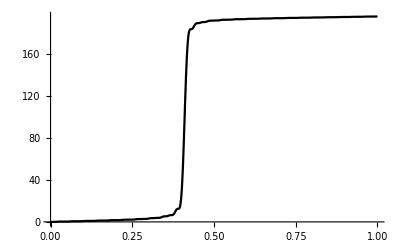

```mathematica
aa6=Transpose[{b,a6}];
q6=ListPlot[aa6,Joined->True,PlotStyle->Black]
```

```mathematica
a7=Table[F[1,1,0.6,50,x],{x,0,1,0.001}]
```

{0.,1.28926×10^-7,4.08836×10^-6,0.0000305799,0.000126162,0.000374665,0.000901728,0.00187367,0.00349054,0.00597371,0.00954922,0.0144283,0.0207867,0.0287459,0.0383563,0.0495861,0.0623164,0.0763423,0.0913816,0.107091,0.123083,0.138955,0.154312,0.168787,0.182072,0.193929,0.204203,0.212826,0.219817,0.225269,0.22934,0.232229,0.234159,0.235356,0.236032,0.236368,0.236508,0.236552,0.23656,0.23656,0.23656,0.236561,0.236573,0.236629,0.236797,0.237186,0.237947,0.23927,0.241371,0.24448,0.24882,0.254586,0.261926,0.270923,0.281582,0.293818,0.30746,0.322253,0.337873,0.353942,0.370057,0.385808,0.400812,0.414728,0.427284,0.438289,0.447637,0.455314,0.461387,0.465992,0.469317,0.471583,0.473022,0.473857,0.474287,0.474474,0.474535,0.474547,0.474547,0.474548,0.474549,0.474551,0.474575,0.474672,0.474935,0.4755,0.476546,0.478284,0.480948,0.484772,0.489972,0.496725,0.505147,0.515278,0.527071,0.540388,0.555001,0.570606,0.586834,0.603279,0.61952,0.635148,0.649792,0.663142,0.674967,0.685124,0.693561,0.700317,0.705507,0.709309,0.711941,0.713641,0.714647,0.715176,0.71541,0.715487,0.715501,0.715501,0.715506,0.715512,0.715514,0.715519,0.71556,0.715713,0.716098,0.716882,0.718273,0.720507,0.723831,0.728483,0.734669,0.742541,0.752178,0.76357,0.776616,0.791118,0.806789,0.82327,0.840153,0.856999,0.873373,0.888871,0.903141,0.915907,0.926983,0.936281,0.943806,0.949652,0.953984,0.95702,0.959006,0.960195,0.960827,0.961107,0.961197,0.961211,0.961213,0.961227,0.96125,0.961267,0.961271,0.961278,0.961344,0.96157,0.962111,0.963169,0.964984,0.967817,0.971929,0.977558,0.984896,0.994063,1.00509,1.01792,1.03239,1.04822,1.06507,1.08252,1.10012,1.11741,1.13392,1.14928,1.16315,1.1753,1.1856,1.19401,1.20061,1.20554,1.20903,1.21134,1.21273,1.21346,1.21379,1.21389,1.2139,1.21391,1.21394,1.214,1.21406,1.21409,1.2141,1.21411,1.21421,1.21453,1.21527,1.21668,1.21902,1.22259,1.22767,1.23447,1.24319,1.2539,1.26657,1.28108,1.29719,1.31455,1.33275,1.35131,1.36972,1.38749,1.40417,1.41938,1.43282,1.4443,1.45377,1.46125,1.46689,1.4709,1.47356,1.47517,1.47602,1.47638,1.47648,1.47649,1.47651,1.47658,1.47671,1.47685,1.47697,1.47704,1.47705,1.47706,1.47721,1.47766,1.47866,1.48052,1.48354,1.48804,1.49432,1.5026,1.51301,1.52559,1.54026,1.5568,1.57488,1.59407,1.61386,1.63371,1.65307,1.6714,1.68827,1.7033,1.71625,1.727,1.73556,1.74205,1.74668,1.74976,1.75161,1.75258,1.75297,1.75307,1.75308,1.75312,1.75327,1.75352,1.75383,1.75412,1.75433,1.75444,1.75445,1.75448,1.75468,1.75531,1.75667,1.75913,1.76304,1.76877,1.77661,1.78677,1.79935,1.81432,1.8315,1.85058,1.8711,1.89254,1.91428,1.93571,1.9562,1.97521,1.9923,2.00713,2.01952,2.02943,2.03698,2.04239,2.04597,2.0481,2.04918,2.0496,2.04968,2.04969,2.0498,2.0501,2.05058,2.05117,2.05179,2.05232,2.05269,2.05285,2.05288,2.05292,2.05321,2.05409,2.05595,2.05923,2.06438,2.07178,2.08173,2.09443,2.10991,2.12805,2.14854,2.17094,2.19465,2.21899,2.24323,2.26665,2.28858,2.30843,2.32579,2.34037,2.35209,2.36104,2.36743,2.37164,2.37411,2.37532,2.37574,2.3758,2.37584,2.37608,2.37665,2.37756,2.3787,2.37994,2.38111,2.38204,2.38265,2.38292,2.38296,2.38302,2.38344,2.38469,2.38729,2.3918,2.39873,2.40854,2.42153,2.43785,2.45744,2.48003,2.50516,2.53216,2.56026,2.58857,2.61621,2.64231,2.66615,2.68711,2.70482,2.71909,2.72998,2.73774,2.74279,2.74568,2.74701,2.74742,2.74745,2.74758,2.74812,2.74924,2.75097,2.75318,2.75563,2.75807,2.76022,2.76186,2.76287,2.76331,2.76339,2.76347,2.76411,2.76595,2.76973,2.77617,2.78592,2.79949,2.81719,2.83909,2.86497,2.89435,2.92648,2.96041,2.99505,3.02925,3.06186,3.09187,3.11843,3.14096,3.15916,3.17301,3.1828,3.18907,3.19253,3.19401,3.19436,3.19439,3.19477,3.19599,3.1983,3.20176,3.20616,3.21117,3.21633,3.22115,3.22519,3.22816,3.22995,3.23071,3.23083,3.23097,3.23199,3.2349,3.24076,3.2506,3.26527,3.2854,3.31126,3.34278,3.37945,3.4204,3.46441,3.51001,3.55559,3.59952,3.64029,3.67662,3.70755,3.73254,3.75148,3.76472,3.77297,3.7773,3.77892,3.77918,3.77933,3.78047,3.7834,3.7886,3.79613,3.80572,3.81677,3.82844,3.83981,3.84999,3.85825,3.86414,3.86761,3.86904,3.86927,3.86952,3.87134,3.87649,3.88671,3.90363,3.92852,3.96221,4.00491,4.05619,4.11495,4.17947,4.24755,4.31665,4.38412,4.44737,4.50415,4.55269,4.5919,4.62143,4.64172,4.65393,4.65984,4.66165,4.66179,4.66266,4.66639,4.67462,4.68837,4.70788,4.73264,4.76147,4.79262,4.82399,4.85345,4.87904,4.8993,4.91346,4.92166,4.925,4.92551,4.92607,4.93017,4.94158,4.96404,5.00085,5.05451,5.1264,5.21659,5.32366,5.4448,5.57591,5.71193,5.84721,5.97601,6.09304,6.19391,6.27557,6.3367,6.37783,6.40138,6.41146,6.41357,6.41407,6.41956,6.43626,6.46934,6.52236,6.59681,6.69189,6.80452,6.9295,7.06009,7.18859,7.30727,7.40923,7.48938,7.54523,7.57754,7.59069,7.59272,7.59497,7.61139,7.6575,7.74903,7.90045,8.1234,8.42525,8.80786,9.26674,9.79076,10.3624,10.9586,11.5526,12.1157,12.6204,13.0429,13.3667,13.5854,13.7056,13.7488,13.7531,13.7733,13.8806,14.1603,14.7095,15.6327,17.0369,19.0266,21.6981,25.1331,29.3943,34.5201,40.5211,47.3779,55.04,63.4266,72.4287,81.9129,91.7261,101.702,111.668,121.451,130.887,139.825,148.135,155.711,162.476,168.385,173.421,177.598,180.957,183.564,185.5,186.863,187.757,188.286,188.555,188.657,188.676,188.68,188.723,188.84,189.051,189.363,189.768,190.251,190.788,191.353,191.919,192.46,192.954,193.386,193.746,194.029,194.237,194.378,194.463,194.506,194.521,194.523,194.525,194.537,194.567,194.618,194.69,194.783,194.89,195.005,195.121,195.232,195.331,195.414,195.479,195.524,195.552,195.565,195.569,195.569,195.572,195.582,195.605,195.644,195.702,195.777,195.87,195.976,196.093,196.214,196.336,196.452,196.559,196.653,196.732,196.795,196.842,196.873,196.893,196.903,196.906,196.906,196.907,196.91,196.917,196.928,196.945,196.966,196.989,197.014,197.038,197.061,197.079,197.093,197.103,197.108,197.11,197.111,197.111,197.114,197.12,197.133,197.153,197.18,197.216,197.26,197.311,197.366,197.424,197.484,197.541,197.596,197.645,197.687,197.722,197.749,197.769,197.783,197.791,197.795,197.796,197.797,197.797,197.798,197.8,197.805,197.811,197.818,197.826,197.833,197.84,197.846,197.851,197.853,197.854,197.855,197.855,197.856,197.858,197.864,197.873,197.886,197.905,197.928,197.956,197.988,198.024,198.061,198.099,198.136,198.172,198.205,198.233,198.258,198.278,198.293,198.304,198.311,198.315,198.317,198.318,198.318,198.318,198.319,198.32,198.322,198.324,198.327,198.33,198.332,198.334,198.335,198.336,198.336,198.336,198.337,198.338,198.341,198.346,198.353,198.364,198.378,198.396,198.417,198.441,198.467,198.495,198.523,198.55,198.577,198.602,198.624,198.643,198.659,198.672,198.681,198.688,198.692,198.694,198.695,198.696,198.696,198.696,198.696,198.697,198.698,198.698,198.7,198.7,198.701,198.701,198.702,198.702,198.702,198.702,198.704,198.707,198.712,198.719,198.728,198.74,198.755,198.772,198.791,198.812,198.835,198.857,198.88,198.902,198.922,198.94,198.956,198.97,198.981,198.989,198.995,199.,199.002,199.004,199.005,199.005,199.005,199.005,199.005,199.005,199.005,199.006,199.006,199.006,199.006,199.006,199.006,199.007,199.008,199.01,199.013,199.017,199.024,199.032,199.043,199.056,199.071,199.088,199.106,199.126,199.145,199.165,199.183,199.201,199.217,199.231,199.243,199.253,199.261,199.266,199.271,199.273,199.275,199.276,199.276,199.276,199.276,199.276,199.276,199.277,199.277,199.277,199.277,199.277,199.277,199.277,199.278,199.279,199.281,199.284,199.289,199.295,199.303,199.314,199.326,199.339,199.355,199.371,199.389,199.406,199.424,199.441,199.457,199.471,199.484,199.495,199.504,199.511,199.517,199.521,199.524,199.525,199.526,199.527,199.527,199.527,199.527,199.527,199.527,199.527,199.527,199.527,199.527,199.527,199.528,199.528,199.53,199.532,199.536,199.54,199.547,199.555,199.565,199.576,199.589,199.604,199.619,199.636,199.652,199.669,199.684,199.699,199.713,199.725,199.735,199.744,199.751,199.756,199.76,199.762,199.764,199.765,199.766,199.766,199.766,199.766,199.766,199.766,199.766,199.766,199.766,199.766,199.766,199.767,199.768,199.769,199.772,199.775,199.78,199.787,199.795,199.805,199.816,199.829,199.843,199.858,199.874,199.89,199.906,199.921,199.936,199.949,199.96,199.97,199.978,199.985,199.99,199.994,199.996,199.998,199.999,200.,200.,200.,200.,200.,200.}

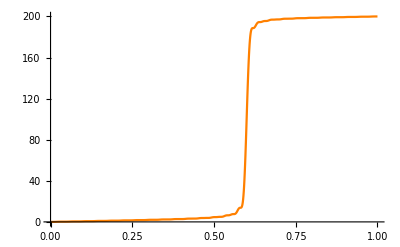

```mathematica
aa7=Transpose[{b,a7}];
q7=ListPlot[aa7,Joined->True,PlotStyle->Orange]
```

```mathematica
a8=Table[F[1,1,0.8,50,x],{x,0,1,0.001}]
```

{0.,1.26824×10^-7,4.022×10^-6,0.0000300871,0.000124149,0.000368766,0.000887761,0.00184522,0.00343876,0.00588747,0.00941563,0.0142335,0.0205175,0.0283905,0.0379065,0.0490387,0.061674,0.0756145,0.0905852,0.106249,0.122225,0.138115,0.153523,0.168086,0.18149,0.193493,0.203933,0.212733,0.219903,0.225529,0.229759,0.232787,0.234831,0.236118,0.236858,0.237236,0.237399,0.237454,0.237466,0.237467,0.237467,0.237467,0.237477,0.237523,0.237667,0.238009,0.238691,0.239895,0.241829,0.244719,0.248788,0.254234,0.261214,0.269826,0.280088,0.291938,0.305225,0.319714,0.3351,0.351023,0.367087,0.382889,0.398043,0.412201,0.425077,0.43646,0.446225,0.454333,0.460829,0.465828,0.469504,0.472066,0.473741,0.474751,0.475299,0.475558,0.475656,0.475682,0.475686,0.475686,0.475686,0.475687,0.475704,0.475776,0.475981,0.476438,0.477309,0.478791,0.481104,0.484479,0.489134,0.495255,0.50298,0.512373,0.523422,0.536023,0.549987,0.565044,0.580858,0.597045,0.613199,0.628913,0.643811,0.657564,0.669913,0.680683,0.689784,0.697217,0.70306,0.70746,0.710612,0.71274,0.714075,0.714838,0.715221,0.715381,0.715431,0.715438,0.715439,0.71544,0.715441,0.715443,0.71547,0.715575,0.715854,0.716446,0.717533,0.719329,0.722065,0.725975,0.731271,0.738126,0.746651,0.756882,0.768766,0.782161,0.796838,0.812489,0.828748,0.84521,0.861455,0.877079,0.891716,0.905058,0.916878,0.927035,0.935479,0.942248,0.947456,0.951279,0.953934,0.955657,0.956683,0.957227,0.957471,0.957555,0.957571,0.957572,0.957576,0.957581,0.957583,0.957587,0.957626,0.957771,0.958138,0.958889,0.960225,0.962377,0.965588,0.970093,0.976097,0.983755,0.993151,1.00429,1.01707,1.03131,1.04675,1.06303,1.07975,1.0965,1.11284,1.12838,1.14274,1.15567,1.16695,1.17649,1.18427,1.19038,1.19497,1.19824,1.20042,1.20177,1.20251,1.20287,1.203,1.20303,1.20303,1.20304,1.20305,1.20307,1.20307,1.20308,1.20313,1.20333,1.2038,1.20473,1.20636,1.20892,1.21267,1.21784,1.22463,1.23318,1.24353,1.25566,1.26942,1.28458,1.30083,1.31778,1.33501,1.35206,1.3685,1.38394,1.39803,1.41051,1.42125,1.43015,1.43728,1.44273,1.44671,1.44944,1.45117,1.45217,1.45267,1.45287,1.45293,1.45293,1.45294,1.45296,1.453,1.45302,1.45302,1.45303,1.45311,1.45336,1.45396,1.45511,1.45707,1.4601,1.46447,1.4704,1.47808,1.48762,1.49905,1.51227,1.5271,1.54327,1.56041,1.57809,1.59586,1.61324,1.62979,1.64512,1.65891,1.67095,1.6811,1.68937,1.69582,1.70061,1.70399,1.70619,1.70751,1.70819,1.70849,1.70857,1.70858,1.70859,1.70863,1.70869,1.70876,1.70879,1.7088,1.70881,1.70891,1.70924,1.70999,1.7114,1.71375,1.71733,1.72241,1.72921,1.73791,1.74858,1.76121,1.77566,1.7917,1.80899,1.82711,1.8456,1.86395,1.88169,1.89835,1.91357,1.92705,1.93861,1.94817,1.95576,1.96152,1.96566,1.96843,1.97013,1.97106,1.97148,1.97161,1.97163,1.97164,1.97169,1.97179,1.97191,1.97202,1.97207,1.97208,1.9721,1.97223,1.97265,1.97358,1.97531,1.97813,1.98236,1.98827,1.99609,2.00597,2.01795,2.03196,2.04782,2.06523,2.08378,2.10301,2.12239,2.1414,2.15953,2.17632,2.19142,2.20456,2.2156,2.22453,2.23142,2.23647,2.23993,2.24212,2.24335,2.24392,2.24412,2.24415,2.24416,2.24423,2.24438,2.24459,2.2448,2.24496,2.24504,2.24506,2.24508,2.24525,2.24577,2.24693,2.24904,2.25244,2.25745,2.26436,2.27339,2.28466,2.29818,2.31381,2.3313,2.35029,2.3703,2.39079,2.4112,2.43095,2.44952,2.46646,2.48143,2.49419,2.50468,2.51292,2.51907,2.52338,2.52616,2.52778,2.52857,2.52885,2.5289,2.52891,2.529,2.52921,2.52953,2.5299,2.53024,2.53048,2.53059,2.53061,2.53064,2.53086,2.53153,2.53297,2.53556,2.53966,2.54563,2.55376,2.56426,2.57722,2.59258,2.61014,2.62958,2.65044,2.67216,2.69414,2.71574,2.73635,2.75542,2.77253,2.78734,2.7997,2.80956,2.81706,2.82241,2.82596,2.82806,2.82913,2.82954,2.82962,2.82963,2.82974,2.83003,2.8305,2.83108,2.83169,2.83221,2.83256,2.83272,2.83275,2.83279,2.83307,2.83392,2.83573,2.83892,2.84391,2.85109,2.86076,2.87309,2.88813,2.90577,2.92571,2.94752,2.97065,2.99445,3.0182,3.04122,3.06285,3.08252,3.09982,3.11446,3.12634,3.13551,3.14219,3.14669,3.14944,3.15087,3.15145,3.15157,3.15158,3.15172,3.15211,3.15278,3.15368,3.15468,3.15564,3.15642,3.15693,3.15716,3.1572,3.15725,3.15761,3.15871,3.161,3.16499,3.17115,3.1799,3.19155,3.20623,3.22395,3.24448,3.26743,3.29224,3.31822,3.3446,3.37056,3.39533,3.4182,3.4386,3.45612,3.47056,3.48188,3.49026,3.49602,3.4996,3.50153,3.50233,3.50252,3.50253,3.5027,3.50323,3.50419,3.50554,3.50714,3.50879,3.51029,3.51146,3.5122,3.51252,3.51258,3.51264,3.51313,3.51456,3.51752,3.5226,3.53035,3.54122,3.55553,3.57338,3.59465,3.61902,3.64595,3.67469,3.7044,3.73413,3.76294,3.78994,3.81439,3.8357,3.85352,3.8677,3.87836,3.88581,3.89053,3.89312,3.89423,3.8945,3.89452,3.89474,3.89548,3.89687,3.89891,3.90143,3.90419,3.90689,3.90923,3.911,3.91209,3.91256,3.91264,3.91272,3.91339,3.91531,3.91923,3.92587,3.9359,3.94981,3.9679,3.9902,4.01648,4.04623,4.07869,4.11289,4.14772,4.18204,4.21472,4.24475,4.27131,4.29382,4.31201,4.32587,4.3357,4.34203,4.34556,4.3471,4.3475,4.34752,4.34784,4.34891,4.35101,4.35416,4.35821,4.36283,4.36759,4.37205,4.37579,4.37854,4.3802,4.3809,4.38101,4.38113,4.38207,4.38476,4.39017,4.39924,4.41277,4.43132,4.45518,4.48425,4.51811,4.55597,4.59672,4.63904,4.68148,4.72256,4.76089,4.79529,4.82486,4.84908,4.86778,4.88122,4.88997,4.8949,4.89708,4.89764,4.89768,4.89817,4.89987,4.90322,4.90839,4.91519,4.92322,4.93184,4.94034,4.94802,4.95429,4.9588,4.96146,4.96256,4.96273,4.96293,4.96435,4.96835,4.97632,4.98955,5.00905,5.0355,5.06913,5.10965,5.15627,5.2077,5.26229,5.3181,5.37309,5.42524,5.47275,5.51417,5.54854,5.5754,5.5949,5.60771,5.61496,5.61814,5.61892,5.61899,5.61991,5.62293,5.62892,5.63824,5.65077,5.66593,5.68275,5.70003,5.7165,5.73096,5.7425,5.75063,5.75535,5.75728,5.75758,5.75791,5.7603,5.76697,5.78011,5.80168,5.83319,5.8755,5.9287,5.9921,6.06414,6.14258,6.22459,6.30703,6.38664,6.46036,6.5256,6.58043,6.62377,6.65548,6.67639,6.68817,6.69319,6.69428,6.69447,6.69663,6.70326,6.71618,6.73638,6.76391,6.79789,6.83663,6.87779,6.91871,6.95669,6.98937,7.01501,7.03279,7.04302,7.04715,7.04779,7.04848,7.05346,7.06727,7.09431,7.1384,7.20235,7.28761,7.39402,7.51972,7.66118,7.81344,7.97048,8.12569,8.27246,8.40476,8.51773,8.60816,8.67485,8.71877,8.74305,8.75274,8.75436,8.75535,8.76329,8.78522,8.82685,8.89194,8.98186,9.09533,9.22846,9.37506,9.5272,9.67604,9.81276,9.92967,10.0212,10.0846,10.1212,10.1361,10.1383,10.1408,10.1592,10.2104,10.3118,10.479,10.7244,11.0555,11.4739,11.9741,12.5434,13.1625,13.806,14.4449,15.0485,15.5873,16.0366,16.3793,16.6095,16.7349,16.7792,16.7834,16.8058,16.9212,17.2189,17.7993,18.7698,20.2395,22.3139,25.0888,28.6442,33.0398,38.3095,44.4587,51.4619,59.2624,67.7728,76.8783,86.4404,96.3021,106.295,116.244,125.979,135.336,144.17,152.354,159.79,166.406,172.163,177.052,181.091,184.327,186.828,188.677,189.972,190.816,191.314,191.564,191.657,191.674,191.679,191.72,191.831,192.03,192.321,192.698,193.143,193.637,194.153,194.667,195.157,195.602,195.989,196.309,196.56,196.744,196.867,196.942,196.979,196.992,196.994,196.995,197.005,197.03,197.072,197.133,197.208,197.295,197.387,197.48,197.566,197.643,197.706,197.753,197.785,197.804,197.812,197.814,197.814,197.818,197.829,197.851,197.886,197.937,198.001,198.078,198.165,198.259,198.356,198.451,198.542,198.624,198.695,198.754,198.8,198.834,198.857,198.87,198.877,198.88,198.88,198.88,198.882,198.886,198.894,198.904,198.916,198.93,198.943,198.956,198.967,198.976,198.982,198.985,198.986,198.986,198.986,198.988,198.993,199.001,199.014,199.033,199.058,199.087,199.121,199.159,199.199,199.24,199.279,199.317,199.352,199.382,199.407,199.427,199.443,199.454,199.461,199.465,199.467,199.467,199.468,199.468,199.468,199.469,199.471,199.473,199.475,199.477,199.478,199.479,199.48,199.48,199.48,199.48,199.481,199.484,199.488,199.494,199.503,199.514,199.529,199.546,199.566,199.587,199.61,199.633,199.656,199.677,199.697,199.715,199.731,199.743,199.754,199.761,199.767,199.77,199.772,199.774,199.774,199.774,199.774,199.774,199.774,199.775,199.775,199.775,199.775,199.775,199.775,199.775,199.776,199.777,199.78,199.783,199.788,199.795,199.804,199.815,199.828,199.842,199.858,199.874,199.891,199.907,199.923,199.938,199.951,199.963,199.973,199.981,199.987,199.992,199.995,199.997,199.999,199.999,200.,200.,200.,200.,200.}

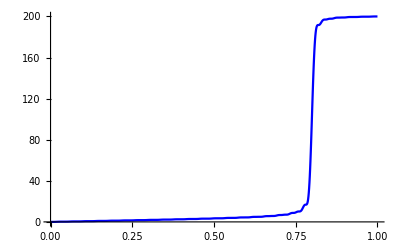

```mathematica
aa8=Transpose[{b,a8}];
q8=ListPlot[aa8,Joined->True,PlotStyle->Blue]
```

```mathematica
a9=Table[F[1,1,24/25,50,x],{x,0,1,0.001}]
```

{0.,1.26321×10^-7,4.00612×10^-6,0.0000299691,0.000123667,0.000367353,0.000884417,0.00183841,0.00342636,0.00586681,0.00938362,0.0141869,0.0204529,0.0283053,0.0377987,0.0489075,0.06152,0.07544,0.0903942,0.106047,0.122019,0.137913,0.153334,0.167918,0.181351,0.193389,0.203869,0.212712,0.219926,0.225594,0.229862,0.232924,0.234997,0.236305,0.23706,0.237449,0.237619,0.237676,0.237689,0.23769,0.23769,0.237691,0.237699,0.237743,0.237881,0.238213,0.238877,0.240053,0.241948,0.244787,0.248792,0.254162,0.261058,0.269578,0.279747,0.291505,0.304707,0.319124,0.334455,0.350342,0.366394,0.382209,0.397399,0.411615,0.424568,0.436043,0.445909,0.454121,0.46072,0.465817,0.469579,0.472215,0.473948,0.475002,0.475581,0.475859,0.475968,0.475998,0.476002,0.476002,0.476003,0.476004,0.476019,0.476085,0.476278,0.476711,0.477543,0.478966,0.481199,0.484471,0.489001,0.494977,0.50254,0.511762,0.522637,0.53507,0.548883,0.563811,0.579528,0.595654,0.611786,0.627522,0.64248,0.656329,0.668804,0.679722,0.688985,0.696582,0.702586,0.707135,0.710417,0.712653,0.714072,0.714897,0.715321,0.715505,0.715566,0.715578,0.715578,0.715579,0.71558,0.715582,0.715605,0.7157,0.715956,0.716508,0.717529,0.719228,0.721834,0.725578,0.730675,0.737302,0.745575,0.755542,0.76716,0.780302,0.79475,0.81021,0.826325,0.842697,0.858912,0.874566,0.889289,0.902769,0.914766,0.925129,0.933795,0.94079,0.946214,0.950235,0.95306,0.954921,0.956053,0.956671,0.956962,0.957071,0.957097,0.957099,0.957101,0.957104,0.957106,0.957109,0.957143,0.957272,0.957604,0.95829,0.959526,0.961534,0.964552,0.968814,0.974529,0.981858,0.990895,1.00166,1.01407,1.02796,1.04307,1.05909,1.07562,1.09224,1.10854,1.12412,1.1386,1.1517,1.16322,1.17302,1.1811,1.1875,1.19235,1.19587,1.19825,1.19977,1.20063,1.20107,1.20125,1.2013,1.20131,1.20131,1.20132,1.20133,1.20133,1.20134,1.20138,1.20155,1.20197,1.20282,1.20429,1.20665,1.21013,1.21496,1.22135,1.22944,1.23931,1.25092,1.26418,1.27887,1.29469,1.3113,1.32826,1.34515,1.36154,1.37703,1.39127,1.40399,1.41501,1.42426,1.43173,1.43754,1.44185,1.44486,1.44684,1.44802,1.44866,1.44894,1.44903,1.44905,1.44905,1.44906,1.44908,1.4491,1.4491,1.44911,1.44917,1.44939,1.44991,1.45094,1.45269,1.45544,1.45943,1.4649,1.47204,1.48097,1.49174,1.50428,1.51845,1.534,1.55058,1.56781,1.58524,1.60241,1.61889,1.63429,1.64827,1.66059,1.67111,1.67979,1.68667,1.69189,1.69565,1.69819,1.69977,1.70066,1.70108,1.70124,1.70127,1.70127,1.70129,1.70133,1.70137,1.70139,1.7014,1.70141,1.70149,1.70177,1.70241,1.70364,1.70571,1.7089,1.71347,1.71966,1.72763,1.73749,1.74925,1.76282,1.77798,1.79446,1.81187,1.82977,1.84769,1.86516,1.88174,1.89705,1.91076,1.92267,1.93267,1.94077,1.94704,1.95167,1.95489,1.95697,1.95819,1.95881,1.95906,1.95912,1.95912,1.95914,1.95919,1.95926,1.95933,1.95937,1.95938,1.9594,1.9595,1.95984,1.96063,1.9621,1.96454,1.96824,1.97347,1.98046,1.98937,2.00027,2.01314,2.02783,2.0441,2.0616,2.07991,2.09854,2.117,2.13479,2.15148,2.16668,2.18011,2.19159,2.20105,2.20855,2.2142,2.21824,2.22094,2.22257,2.22345,2.22384,2.22395,2.22396,2.22398,2.22404,2.22415,2.22428,2.22439,2.22445,2.22446,2.22448,2.22461,2.22503,2.22599,2.22775,2.23062,2.2349,2.24089,2.2488,2.25877,2.27086,2.28497,2.30093,2.31843,2.33706,2.35636,2.3758,2.39484,2.41299,2.42979,2.44488,2.45801,2.46903,2.47793,2.4848,2.48983,2.49328,2.49545,2.49667,2.49725,2.49744,2.49747,2.49748,2.49755,2.4977,2.49791,2.49812,2.49828,2.49836,2.49838,2.4984,2.49856,2.49909,2.50024,2.50234,2.50571,2.51069,2.51756,2.52653,2.53774,2.55117,2.56671,2.5841,2.60299,2.6229,2.64331,2.66364,2.68334,2.70187,2.7188,2.73378,2.74658,2.75711,2.76542,2.77164,2.77602,2.77887,2.78055,2.78138,2.7817,2.78176,2.78176,2.78184,2.78203,2.78232,2.78266,2.78298,2.78321,2.78332,2.78334,2.78336,2.78357,2.78422,2.78561,2.78812,2.79209,2.79789,2.8058,2.81603,2.82866,2.84366,2.86085,2.8799,2.90038,2.92176,2.94342,2.96477,2.98519,3.00416,3.02123,3.03608,3.04852,3.05853,3.0662,3.07174,3.07546,3.07772,3.07891,3.07941,3.07953,3.07954,3.07961,3.07983,3.08022,3.08072,3.08126,3.08172,3.08204,3.08219,3.08221,3.08225,3.08251,3.0833,3.08499,3.08799,3.09269,3.09948,3.10863,3.12035,3.13469,3.15155,3.17067,3.19166,3.214,3.23706,3.26019,3.28269,3.30395,3.32341,3.34063,3.35534,3.36739,3.37683,3.38381,3.38863,3.39168,3.39336,3.39411,3.39433,3.39435,3.39441,3.39466,3.39516,3.39586,3.39667,3.39746,3.39812,3.39856,3.39876,3.3988,3.39884,3.39917,3.40015,3.40221,3.40582,3.41142,3.41941,3.43009,3.44362,3.46002,3.47911,3.50056,3.52386,3.5484,3.57346,3.59829,3.62216,3.64438,3.66441,3.68181,3.69635,3.70797,3.71677,3.72302,3.72709,3.72944,3.73057,3.73094,3.73099,3.73104,3.73131,3.73191,3.73284,3.73401,3.73526,3.73643,3.73736,3.73796,3.73823,3.73827,3.73832,3.73874,3.73995,3.74249,3.74687,3.7536,3.7631,3.77568,3.79147,3.8104,3.83224,3.85653,3.88266,3.90987,3.93734,3.96423,3.98971,4.01308,4.03377,4.05138,4.06574,4.07686,4.08496,4.0904,4.09367,4.09534,4.09596,4.09607,4.0961,4.09638,4.0971,4.09831,4.09992,4.10179,4.10367,4.10536,4.10666,4.10748,4.10784,4.1079,4.10797,4.10849,4.11002,4.11317,4.11855,4.12674,4.13819,4.1532,4.17185,4.19401,4.21932,4.24718,4.27683,4.30737,4.33783,4.36724,4.39471,4.41947,4.44096,4.45882,4.47296,4.48351,4.49081,4.49537,4.49781,4.49882,4.49904,4.49907,4.49935,4.50019,4.50172,4.50391,4.50659,4.50949,4.51231,4.51474,4.51657,4.5177,4.51818,4.51826,4.51835,4.51902,4.52098,4.52495,4.53167,4.5418,4.55582,4.57403,4.59645,4.62283,4.65265,4.68515,4.71936,4.75417,4.78845,4.82106,4.85102,4.87752,4.9,4.91817,4.93205,4.94192,4.94831,4.95191,4.95351,4.95395,4.95398,4.95424,4.95521,4.95714,4.96008,4.96388,4.96822,4.97271,4.97692,4.98046,4.98305,4.98462,4.98528,4.98539,4.98551,4.9864,4.98894,4.99406,5.00265,5.01545,5.03302,5.05562,5.08319,5.11531,5.15125,5.19001,5.23032,5.27084,5.31018,5.34702,5.38024,5.40899,5.43274,5.4513,5.46485,5.47392,5.47925,5.4818,5.48261,5.48268,5.48292,5.48404,5.48648,5.49043,5.4958,5.50225,5.50928,5.51627,5.52264,5.52787,5.53164,5.53388,5.53481,5.53495,5.53511,5.53632,5.53973,5.54653,5.55783,5.57452,5.59723,5.62616,5.66111,5.70144,5.74611,5.79373,5.84268,5.8912,5.9376,5.98029,6.018,6.0498,6.07525,6.09432,6.10746,6.11553,6.11963,6.1211,6.1213,6.1215,6.12279,6.12592,6.13133,6.13903,6.14871,6.15974,6.17128,6.18244,6.19235,6.20033,6.20598,6.20929,6.21065,6.21086,6.2111,6.2128,6.21756,6.22699,6.2425,6.26524,6.29587,6.33456,6.38086,6.43376,6.49173,6.55281,6.61479,6.67535,6.73228,6.78364,6.82791,6.86415,6.89201,6.9118,6.9244,6.93118,6.93388,6.93437,6.93454,6.93604,6.94021,6.94787,6.95933,6.97434,6.99213,7.01159,7.03134,7.04996,7.06617,7.079,7.08797,7.09315,7.09525,7.09557,7.09592,7.09848,7.10557,7.11948,7.1422,7.17521,7.21933,7.27455,7.34004,7.41413,7.49443,7.57805,7.66173,7.74223,7.8165,7.88199,7.93686,7.98014,8.01178,8.03265,8.04447,8.04958,8.05076,8.0509,8.05277,8.05868,8.07033,8.08859,8.11348,8.14413,8.17896,8.21583,8.25233,8.28606,8.31493,8.33747,8.35304,8.36194,8.36552,8.36606,8.36665,8.37089,8.38257,8.40533,8.44223,8.49548,8.56611,8.65384,8.75699,8.8726,8.99662,9.12418,9.25008,9.36915,9.47676,9.56919,9.64403,9.70034,9.73878,9.76155,9.77214,9.77503,9.77525,9.77785,9.78744,9.8077,9.84102,9.88824,9.94857,10.0197,10.0979,10.1788,10.2574,10.3289,10.3894,10.4361,10.4682,10.4864,10.4936,10.4947,10.4959,10.5044,10.5277,10.5729,10.6459,10.7509,10.8895,11.0608,11.2611,11.4842,11.7215,11.9632,12.1988,12.418,12.6118,12.7734,12.899,12.9877,13.0425,13.0696,13.0779,13.0786,13.0836,13.1049,13.153,13.2362,13.359,13.5224,13.7228,13.9527,14.2014,14.4554,14.7005,14.923,15.1111,15.2568,15.3569,15.414,15.437,15.4405,15.4443,15.4719,15.5485,15.6988,15.9445,16.3022,16.7807,17.38,18.0901,18.891,19.7535,20.6411,21.5131,22.3275,23.0454,23.6355,24.0779,24.3684,24.5213,24.5716,24.5757,24.6109,24.773,25.1729,25.9314,27.1731,29.02,31.5838,34.9595,39.2184,44.4031,50.5235,57.5538,65.4331,74.0658,83.3257,93.0608,103.1,113.26,123.354,133.201,142.63,151.493,159.664,167.048,173.583,179.238,184.014,187.944,191.082,193.506,195.304,196.575,197.422,197.942,198.226,198.355,198.395,198.399,198.406,198.437,198.507,198.615,198.759,198.926,199.105,199.284,199.452,199.6,199.724,199.82,199.892,199.94,199.971,199.988,199.996,199.999,200.,200.,200.}

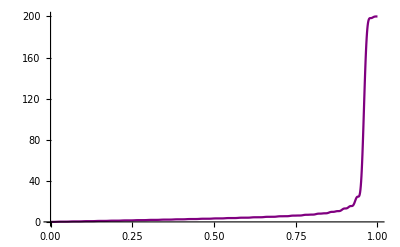

```mathematica
aa9=Transpose[{b,a9}];
q9=ListPlot[aa9,Joined->True,PlotRange->All,PlotStyle->Purple]
```

```mathematica
a10=Table[F[1,1,0.3,50,x],{x,0,1,0.001}]
```

{0.,0.0159281,0.0314303,0.0461091,0.0596211,0.071698,0.0821606,0.0909255,0.0980035,0.10349,0.107549,0.110392,0.112259,0.113388,0.114003,0.114293,0.114403,0.114432,0.114435,0.114435,0.114436,0.114437,0.114457,0.114541,0.11478,0.115311,0.116317,0.118023,0.120674,0.124522,0.129799,0.136694,0.145331,0.155749,0.167891,0.181598,0.196614,0.212597,0.229141,0.2458,0.262118,0.277662,0.292046,0.304962,0.316193,0.325624,0.333245,0.339142,0.343479,0.346484,0.348414,0.349537,0.350106,0.350337,0.350399,0.350404,0.350412,0.350441,0.350478,0.350503,0.350509,0.350518,0.350604,0.350895,0.351582,0.352908,0.355158,0.358632,0.363626,0.370396,0.379131,0.389931,0.402784,0.417559,0.434002,0.451751,0.47035,0.489283,0.508009,0.525993,0.542749,0.557874,0.571067,0.582154,0.591088,0.597946,0.602914,0.606263,0.608313,0.609406,0.609872,0.609996,0.610005,0.610046,0.610192,0.610446,0.610762,0.611069,0.611297,0.611409,0.611429,0.611457,0.61168,0.612373,0.613884,0.616612,0.620973,0.62736,0.636106,0.647441,0.661461,0.678105,0.697148,0.718198,0.740724,0.764084,0.787567,0.810446,0.832029,0.851712,0.86902,0.883637,0.895428,0.904439,0.910881,0.915103,0.91755,0.918717,0.919098,0.919141,0.919204,0.919534,0.92025,0.921351,0.922731,0.924217,0.925605,0.926715,0.927434,0.927755,0.927808,0.927873,0.928376,0.929863,0.932962,0.938329,0.946585,0.958248,0.973675,0.993011,1.01615,1.04274,1.07215,1.10356,1.13597,1.1683,1.19946,1.22842,1.25431,1.27649,1.29459,1.30851,1.31847,1.32492,1.32853,1.33011,1.33051,1.33054,1.3309,1.33212,1.3345,1.33809,1.34272,1.34803,1.35354,1.35873,1.36312,1.36636,1.36833,1.36916,1.36929,1.36945,1.37059,1.37388,1.38052,1.3917,1.40844,1.43147,1.46114,1.49735,1.53954,1.58665,1.63725,1.68956,1.74167,1.7916,1.83754,1.87798,1.91181,1.93845,1.95791,1.97073,1.97797,1.9811,1.98182,1.98191,1.98305,1.98663,1.99365,2.00457,2.0193,2.0372,2.0572,2.0779,2.09777,2.11536,2.12952,2.13956,2.14546,2.14788,2.14826,2.14868,2.15177,2.16044,2.17766,2.20615,2.24803,2.30464,2.37625,2.46202,2.55989,2.66678,2.7787,2.89112,2.99931,3.09877,3.18567,3.25719,3.31185,3.3497,3.37237,3.38296,3.38579,3.38602,3.38917,3.40056,3.42474,3.46501,3.52302,3.59848,3.68916,3.79098,3.89844,4.00511,4.10441,4.19033,4.25832,4.30599,4.33372,4.34507,4.34683,4.34879,4.3632,4.40383,4.48486,4.61951,4.81865,5.08943,5.43413,5.84933,6.32547,6.84709,7.3935,7.9402,8.46083,8.92957,9.32397,9.62795,9.8347,9.94941,9.99142,9.99579,10.0139,10.1128,10.3743,10.8917,11.7664,13.1037,15.0071,17.5733,20.8859,25.0107,29.9905,35.8415,42.5502,50.0727,58.3346,67.2327,76.6387,86.4034,96.363,106.345,116.177,125.691,134.733,143.167,150.882,157.795,163.853,169.034,173.346,176.828,179.539,181.561,182.99,183.932,184.493,184.78,184.89,184.911,184.915,184.959,185.081,185.304,185.636,186.068,186.586,187.165,187.777,188.391,188.981,189.523,189.998,190.394,190.707,190.939,191.097,191.192,191.24,191.257,191.26,191.262,191.276,191.31,191.368,191.453,191.561,191.687,191.823,191.962,192.095,192.216,192.318,192.399,192.457,192.493,192.512,192.518,192.519,192.521,192.531,192.554,192.597,192.66,192.745,192.851,192.974,193.11,193.253,193.398,193.537,193.666,193.781,193.877,193.955,194.012,194.052,194.076,194.089,194.093,194.094,194.094,194.098,194.107,194.123,194.145,194.173,194.206,194.242,194.277,194.309,194.338,194.36,194.377,194.387,194.392,194.393,194.393,194.395,194.4,194.412,194.433,194.463,194.504,194.555,194.615,194.683,194.755,194.83,194.904,194.974,195.038,195.094,195.141,195.178,195.206,195.225,195.236,195.242,195.244,195.244,195.245,195.246,195.25,195.257,195.267,195.279,195.292,195.306,195.319,195.331,195.341,195.347,195.351,195.353,195.354,195.354,195.355,195.359,195.367,195.38,195.399,195.425,195.457,195.496,195.539,195.587,195.636,195.686,195.734,195.78,195.821,195.856,195.885,195.908,195.924,195.936,195.942,195.946,195.947,195.947,195.947,195.948,195.95,195.954,195.959,195.965,195.971,195.978,195.984,195.988,195.992,195.994,195.995,195.995,195.995,195.996,195.999,196.005,196.014,196.028,196.046,196.069,196.097,196.129,196.164,196.201,196.239,196.277,196.313,196.346,196.375,196.4,196.42,196.436,196.447,196.455,196.459,196.462,196.462,196.462,196.462,196.463,196.464,196.466,196.469,196.473,196.476,196.479,196.482,196.484,196.485,196.485,196.485,196.485,196.486,196.488,196.493,196.5,196.51,196.524,196.542,196.564,196.589,196.617,196.647,196.678,196.709,196.739,196.767,196.793,196.816,196.834,196.85,196.861,196.87,196.875,196.878,196.88,196.88,196.88,196.88,196.881,196.882,196.883,196.884,196.886,196.888,196.89,196.891,196.891,196.892,196.892,196.892,196.893,196.894,196.898,196.903,196.912,196.923,196.937,196.955,196.975,196.998,197.023,197.05,197.076,197.103,197.128,197.152,197.172,197.191,197.206,197.217,197.226,197.233,197.237,197.239,197.24,197.241,197.241,197.241,197.241,197.241,197.242,197.243,197.244,197.245,197.246,197.246,197.246,197.246,197.247,197.247,197.248,197.251,197.256,197.262,197.272,197.283,197.298,197.315,197.335,197.357,197.38,197.403,197.427,197.45,197.472,197.492,197.509,197.524,197.536,197.546,197.553,197.558,197.561,197.563,197.564,197.564,197.564,197.564,197.564,197.564,197.565,197.566,197.566,197.567,197.567,197.567,197.567,197.567,197.567,197.569,197.571,197.574,197.58,197.588,197.597,197.61,197.625,197.642,197.661,197.681,197.703,197.724,197.746,197.766,197.785,197.802,197.817,197.83,197.84,197.848,197.853,197.857,197.86,197.861,197.862,197.862,197.862,197.862,197.862,197.862,197.863,197.863,197.863,197.863,197.864,197.864,197.864,197.864,197.865,197.867,197.87,197.874,197.881,197.889,197.9,197.913,197.928,197.945,197.963,197.982,198.002,198.023,198.042,198.06,198.077,198.092,198.105,198.116,198.124,198.131,198.136,198.139,198.141,198.142,198.142,198.142,198.142,198.142,198.143,198.143,198.143,198.143,198.143,198.143,198.143,198.143,198.143,198.144,198.146,198.148,198.152,198.157,198.165,198.174,198.185,198.198,198.213,198.23,198.248,198.267,198.286,198.304,198.322,198.339,198.354,198.367,198.379,198.388,198.395,198.401,198.404,198.407,198.409,198.409,198.41,198.41,198.41,198.41,198.41,198.41,198.41,198.41,198.41,198.41,198.41,198.41,198.411,198.412,198.414,198.417,198.422,198.428,198.436,198.446,198.458,198.472,198.487,198.503,198.521,198.539,198.557,198.574,198.591,198.606,198.62,198.631,198.641,198.649,198.656,198.66,198.663,198.665,198.667,198.667,198.667,198.668,198.668,198.668,198.668,198.668,198.668,198.668,198.668,198.668,198.668,198.668,198.669,198.671,198.673,198.677,198.683,198.69,198.698,198.709,198.721,198.735,198.751,198.767,198.784,198.802,198.819,198.835,198.851,198.865,198.877,198.887,198.896,198.903,198.908,198.912,198.915,198.916,198.917,198.918,198.918,198.918,198.918,198.918,198.918,198.918,198.918,198.918,198.918,198.918,198.919,198.919,198.921,198.923,198.926,198.931,198.937,198.944,198.954,198.965,198.978,198.992,199.008,199.024,199.041,199.058,199.074,199.09,199.104,199.117,199.128,199.137,199.145,199.151,199.155,199.159,199.161,199.162,199.163,199.163,199.163,199.163,199.163,199.163,199.164,199.164,199.164,199.164,199.164,199.164,199.164,199.165,199.167,199.17,199.174,199.179,199.186,199.194,199.204,199.216,199.23,199.244,199.26,199.276,199.293,199.309,199.324,199.339,199.352,199.364,199.374,199.383,199.39,199.395,199.399,199.401,199.403,199.404,199.405,199.405,199.405,199.405,199.405,199.405,199.405,199.405,199.405,199.405,199.405,199.406,199.406,199.408,199.41,199.413,199.418,199.424,199.431,199.441,199.452,199.464,199.478,199.493,199.508,199.525,199.541,199.556,199.571,199.585,199.598,199.608,199.618,199.625,199.631,199.636,199.639,199.641,199.642,199.643,199.644,199.644,199.644,199.644,199.644,199.644,199.644,199.644,199.644,199.644,199.644,199.645,199.646,199.648,199.651,199.655,199.66,199.666,199.675,199.685,199.696,199.709,199.724,199.739,199.755,199.771,199.787,199.802,199.816,199.829,199.841,199.851,199.859,199.866,199.871,199.875,199.878,199.879,199.88,199.881,199.881,199.881,199.881,199.881,199.881,199.881,199.881,199.882,199.882,199.882,199.882,199.883,199.884,199.887,199.89,199.894,199.9,199.908,199.917,199.928,199.94,199.954,199.969,199.984,200.}

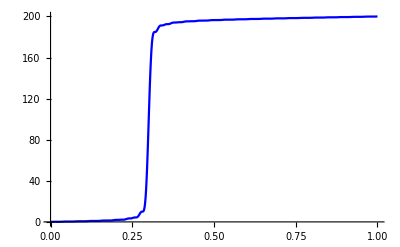

```mathematica
aa10=Transpose[{b,a10}];
q10=ListPlot[aa10,Joined->True,PlotRange->All,PlotStyle->Blue]
```

```mathematica
a11=Table[F[1,1,0.6,50,x],{x,0,1,0.001}]
```

{0.,1.28926×10^-7,4.08836×10^-6,0.0000305799,0.000126162,0.000374665,0.000901728,0.00187367,0.00349054,0.00597371,0.00954922,0.0144283,0.0207867,0.0287459,0.0383563,0.0495861,0.0623164,0.0763423,0.0913816,0.107091,0.123083,0.138955,0.154312,0.168787,0.182072,0.193929,0.204203,0.212826,0.219817,0.225269,0.22934,0.232229,0.234159,0.235356,0.236032,0.236368,0.236508,0.236552,0.23656,0.23656,0.23656,0.236561,0.236573,0.236629,0.236797,0.237186,0.237947,0.23927,0.241371,0.24448,0.24882,0.254586,0.261926,0.270923,0.281582,0.293818,0.30746,0.322253,0.337873,0.353942,0.370057,0.385808,0.400812,0.414728,0.427284,0.438289,0.447637,0.455314,0.461387,0.465992,0.469317,0.471583,0.473022,0.473857,0.474287,0.474474,0.474535,0.474547,0.474547,0.474548,0.474549,0.474551,0.474575,0.474672,0.474935,0.4755,0.476546,0.478284,0.480948,0.484772,0.489972,0.496725,0.505147,0.515278,0.527071,0.540388,0.555001,0.570606,0.586834,0.603279,0.61952,0.635148,0.649792,0.663142,0.674967,0.685124,0.693561,0.700317,0.705507,0.709309,0.711941,0.713641,0.714647,0.715176,0.71541,0.715487,0.715501,0.715501,0.715506,0.715512,0.715514,0.715519,0.71556,0.715713,0.716098,0.716882,0.718273,0.720507,0.723831,0.728483,0.734669,0.742541,0.752178,0.76357,0.776616,0.791118,0.806789,0.82327,0.840153,0.856999,0.873373,0.888871,0.903141,0.915907,0.926983,0.936281,0.943806,0.949652,0.953984,0.95702,0.959006,0.960195,0.960827,0.961107,0.961197,0.961211,0.961213,0.961227,0.96125,0.961267,0.961271,0.961278,0.961344,0.96157,0.962111,0.963169,0.964984,0.967817,0.971929,0.977558,0.984896,0.994063,1.00509,1.01792,1.03239,1.04822,1.06507,1.08252,1.10012,1.11741,1.13392,1.14928,1.16315,1.1753,1.1856,1.19401,1.20061,1.20554,1.20903,1.21134,1.21273,1.21346,1.21379,1.21389,1.2139,1.21391,1.21394,1.214,1.21406,1.21409,1.2141,1.21411,1.21421,1.21453,1.21527,1.21668,1.21902,1.22259,1.22767,1.23447,1.24319,1.2539,1.26657,1.28108,1.29719,1.31455,1.33275,1.35131,1.36972,1.38749,1.40417,1.41938,1.43282,1.4443,1.45377,1.46125,1.46689,1.4709,1.47356,1.47517,1.47602,1.47638,1.47648,1.47649,1.47651,1.47658,1.47671,1.47685,1.47697,1.47704,1.47705,1.47706,1.47721,1.47766,1.47866,1.48052,1.48354,1.48804,1.49432,1.5026,1.51301,1.52559,1.54026,1.5568,1.57488,1.59407,1.61386,1.63371,1.65307,1.6714,1.68827,1.7033,1.71625,1.727,1.73556,1.74205,1.74668,1.74976,1.75161,1.75258,1.75297,1.75307,1.75308,1.75312,1.75327,1.75352,1.75383,1.75412,1.75433,1.75444,1.75445,1.75448,1.75468,1.75531,1.75667,1.75913,1.76304,1.76877,1.77661,1.78677,1.79935,1.81432,1.8315,1.85058,1.8711,1.89254,1.91428,1.93571,1.9562,1.97521,1.9923,2.00713,2.01952,2.02943,2.03698,2.04239,2.04597,2.0481,2.04918,2.0496,2.04968,2.04969,2.0498,2.0501,2.05058,2.05117,2.05179,2.05232,2.05269,2.05285,2.05288,2.05292,2.05321,2.05409,2.05595,2.05923,2.06438,2.07178,2.08173,2.09443,2.10991,2.12805,2.14854,2.17094,2.19465,2.21899,2.24323,2.26665,2.28858,2.30843,2.32579,2.34037,2.35209,2.36104,2.36743,2.37164,2.37411,2.37532,2.37574,2.3758,2.37584,2.37608,2.37665,2.37756,2.3787,2.37994,2.38111,2.38204,2.38265,2.38292,2.38296,2.38302,2.38344,2.38469,2.38729,2.3918,2.39873,2.40854,2.42153,2.43785,2.45744,2.48003,2.50516,2.53216,2.56026,2.58857,2.61621,2.64231,2.66615,2.68711,2.70482,2.71909,2.72998,2.73774,2.74279,2.74568,2.74701,2.74742,2.74745,2.74758,2.74812,2.74924,2.75097,2.75318,2.75563,2.75807,2.76022,2.76186,2.76287,2.76331,2.76339,2.76347,2.76411,2.76595,2.76973,2.77617,2.78592,2.79949,2.81719,2.83909,2.86497,2.89435,2.92648,2.96041,2.99505,3.02925,3.06186,3.09187,3.11843,3.14096,3.15916,3.17301,3.1828,3.18907,3.19253,3.19401,3.19436,3.19439,3.19477,3.19599,3.1983,3.20176,3.20616,3.21117,3.21633,3.22115,3.22519,3.22816,3.22995,3.23071,3.23083,3.23097,3.23199,3.2349,3.24076,3.2506,3.26527,3.2854,3.31126,3.34278,3.37945,3.4204,3.46441,3.51001,3.55559,3.59952,3.64029,3.67662,3.70755,3.73254,3.75148,3.76472,3.77297,3.7773,3.77892,3.77918,3.77933,3.78047,3.7834,3.7886,3.79613,3.80572,3.81677,3.82844,3.83981,3.84999,3.85825,3.86414,3.86761,3.86904,3.86927,3.86952,3.87134,3.87649,3.88671,3.90363,3.92852,3.96221,4.00491,4.05619,4.11495,4.17947,4.24755,4.31665,4.38412,4.44737,4.50415,4.55269,4.5919,4.62143,4.64172,4.65393,4.65984,4.66165,4.66179,4.66266,4.66639,4.67462,4.68837,4.70788,4.73264,4.76147,4.79262,4.82399,4.85345,4.87904,4.8993,4.91346,4.92166,4.925,4.92551,4.92607,4.93017,4.94158,4.96404,5.00085,5.05451,5.1264,5.21659,5.32366,5.4448,5.57591,5.71193,5.84721,5.97601,6.09304,6.19391,6.27557,6.3367,6.37783,6.40138,6.41146,6.41357,6.41407,6.41956,6.43626,6.46934,6.52236,6.59681,6.69189,6.80452,6.9295,7.06009,7.18859,7.30727,7.40923,7.48938,7.54523,7.57754,7.59069,7.59272,7.59497,7.61139,7.6575,7.74903,7.90045,8.1234,8.42525,8.80786,9.26674,9.79076,10.3624,10.9586,11.5526,12.1157,12.6204,13.0429,13.3667,13.5854,13.7056,13.7488,13.7531,13.7733,13.8806,14.1603,14.7095,15.6327,17.0369,19.0266,21.6981,25.1331,29.3943,34.5201,40.5211,47.3779,55.04,63.4266,72.4287,81.9129,91.7261,101.702,111.668,121.451,130.887,139.825,148.135,155.711,162.476,168.385,173.421,177.598,180.957,183.564,185.5,186.863,187.757,188.286,188.555,188.657,188.676,188.68,188.723,188.84,189.051,189.363,189.768,190.251,190.788,191.353,191.919,192.46,192.954,193.386,193.746,194.029,194.237,194.378,194.463,194.506,194.521,194.523,194.525,194.537,194.567,194.618,194.69,194.783,194.89,195.005,195.121,195.232,195.331,195.414,195.479,195.524,195.552,195.565,195.569,195.569,195.572,195.582,195.605,195.644,195.702,195.777,195.87,195.976,196.093,196.214,196.336,196.452,196.559,196.653,196.732,196.795,196.842,196.873,196.893,196.903,196.906,196.906,196.907,196.91,196.917,196.928,196.945,196.966,196.989,197.014,197.038,197.061,197.079,197.093,197.103,197.108,197.11,197.111,197.111,197.114,197.12,197.133,197.153,197.18,197.216,197.26,197.311,197.366,197.424,197.484,197.541,197.596,197.645,197.687,197.722,197.749,197.769,197.783,197.791,197.795,197.796,197.797,197.797,197.798,197.8,197.805,197.811,197.818,197.826,197.833,197.84,197.846,197.851,197.853,197.854,197.855,197.855,197.856,197.858,197.864,197.873,197.886,197.905,197.928,197.956,197.988,198.024,198.061,198.099,198.136,198.172,198.205,198.233,198.258,198.278,198.293,198.304,198.311,198.315,198.317,198.318,198.318,198.318,198.319,198.32,198.322,198.324,198.327,198.33,198.332,198.334,198.335,198.336,198.336,198.336,198.337,198.338,198.341,198.346,198.353,198.364,198.378,198.396,198.417,198.441,198.467,198.495,198.523,198.55,198.577,198.602,198.624,198.643,198.659,198.672,198.681,198.688,198.692,198.694,198.695,198.696,198.696,198.696,198.696,198.697,198.698,198.698,198.7,198.7,198.701,198.701,198.702,198.702,198.702,198.702,198.704,198.707,198.712,198.719,198.728,198.74,198.755,198.772,198.791,198.812,198.835,198.857,198.88,198.902,198.922,198.94,198.956,198.97,198.981,198.989,198.995,199.,199.002,199.004,199.005,199.005,199.005,199.005,199.005,199.005,199.005,199.006,199.006,199.006,199.006,199.006,199.006,199.007,199.008,199.01,199.013,199.017,199.024,199.032,199.043,199.056,199.071,199.088,199.106,199.126,199.145,199.165,199.183,199.201,199.217,199.231,199.243,199.253,199.261,199.266,199.271,199.273,199.275,199.276,199.276,199.276,199.276,199.276,199.276,199.277,199.277,199.277,199.277,199.277,199.277,199.277,199.278,199.279,199.281,199.284,199.289,199.295,199.303,199.314,199.326,199.339,199.355,199.371,199.389,199.406,199.424,199.441,199.457,199.471,199.484,199.495,199.504,199.511,199.517,199.521,199.524,199.525,199.526,199.527,199.527,199.527,199.527,199.527,199.527,199.527,199.527,199.527,199.527,199.527,199.528,199.528,199.53,199.532,199.536,199.54,199.547,199.555,199.565,199.576,199.589,199.604,199.619,199.636,199.652,199.669,199.684,199.699,199.713,199.725,199.735,199.744,199.751,199.756,199.76,199.762,199.764,199.765,199.766,199.766,199.766,199.766,199.766,199.766,199.766,199.766,199.766,199.766,199.766,199.767,199.768,199.769,199.772,199.775,199.78,199.787,199.795,199.805,199.816,199.829,199.843,199.858,199.874,199.89,199.906,199.921,199.936,199.949,199.96,199.97,199.978,199.985,199.99,199.994,199.996,199.998,199.999,200.,200.,200.,200.,200.,200.}

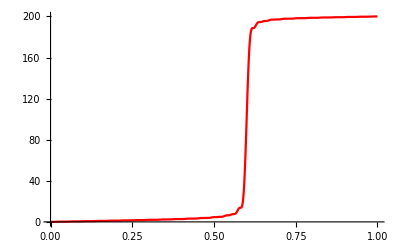

```mathematica
aa11=Transpose[{b,a11}];
q11=ListPlot[aa11,Joined->True,PlotRange->All,PlotStyle->Red]
```

```mathematica
a12=Table[F[1,1,0.61,50,x],{x,0,1,0.001}]
```

{0.,0.000360204,0.000763153,0.0012575,0.00190292,0.00277358,0.00395958,0.0055658,0.00770827,0.0105081,0.0140834,0.0185405,0.0239637,0.0304069,0.0378856,0.0463715,0.0557901,0.0660214,0.0769038,0.0882414,0.0998138,0.111388,0.122729,0.133618,0.143857,0.153284,0.161779,0.169265,0.175715,0.181142,0.1856,0.189174,0.19197,0.194107,0.195706,0.196883,0.197745,0.198381,0.198866,0.199259,0.19961,0.19996,0.200352,0.200834,0.201466,0.202323,0.203494,0.205085,0.207215,0.210006,0.213578,0.218039,0.223477,0.229946,0.237465,0.246006,0.255494,0.265808,0.276787,0.28823,0.299915,0.311604,0.32306,0.334058,0.344397,0.353911,0.362478,0.370021,0.376509,0.381958,0.386424,0.389992,0.392771,0.394883,0.396452,0.397598,0.398427,0.399031,0.399485,0.399849,0.40017,0.400491,0.400852,0.4013,0.401897,0.402715,0.403847,0.405402,0.4075,0.410268,0.413831,0.418303,0.423774,0.430304,0.437914,0.446576,0.456216,0.466712,0.477895,0.489562,0.501481,0.513408,0.525096,0.536313,0.546851,0.556538,0.565247,0.572897,0.57946,0.584951,0.58943,0.592986,0.595735,0.597802,0.599319,0.600408,0.60118,0.601729,0.602132,0.602447,0.602721,0.602993,0.603304,0.603699,0.604236,0.604992,0.606061,0.607555,0.609601,0.612332,0.615881,0.620369,0.625895,0.632525,0.640281,0.649141,0.659028,0.669815,0.681327,0.693351,0.705644,0.717949,0.730006,0.741569,0.752419,0.762376,0.771305,0.779123,0.785801,0.791357,0.795855,0.799395,0.802097,0.804098,0.805537,0.806544,0.807235,0.807708,0.808039,0.808288,0.808498,0.808707,0.80895,0.809271,0.809728,0.810397,0.811377,0.812784,0.814755,0.817433,0.820961,0.825474,0.831079,0.837853,0.845825,0.854973,0.865219,0.876431,0.888423,0.900967,0.913805,0.926658,0.939249,0.951313,0.962615,0.972961,0.982206,0.990265,0.997106,1.00275,1.00728,1.0108,1.01343,1.01534,1.01668,1.01758,1.01816,1.01854,1.01878,1.01895,1.01908,1.01922,1.01938,1.01961,1.01997,1.02053,1.02139,1.02268,1.02455,1.02716,1.03066,1.0352,1.04092,1.04789,1.05617,1.06572,1.07647,1.08827,1.10094,1.11422,1.12782,1.14144,1.15478,1.16754,1.17948,1.19037,1.20005,1.20844,1.21551,1.22129,1.22585,1.22933,1.23189,1.23368,1.23487,1.23563,1.23609,1.23635,1.23649,1.23658,1.23664,1.2367,1.23678,1.23692,1.23716,1.23758,1.23829,1.23944,1.24118,1.24368,1.24715,1.25174,1.25761,1.26486,1.27354,1.28365,1.2951,1.30773,1.32134,1.33563,1.35029,1.36499,1.37937,1.39311,1.40592,1.41756,1.42785,1.4367,1.44408,1.45003,1.45465,1.45808,1.46052,1.46216,1.46318,1.46377,1.46408,1.46422,1.46428,1.4643,1.4643,1.46431,1.46432,1.46437,1.46449,1.46476,1.4653,1.46626,1.46783,1.47021,1.47362,1.47828,1.48435,1.49198,1.50124,1.51212,1.52455,1.53834,1.55325,1.56897,1.58513,1.60134,1.61719,1.6323,1.64634,1.65903,1.67018,1.67967,1.68747,1.69366,1.69835,1.70173,1.70402,1.70545,1.70627,1.70667,1.70682,1.70686,1.70686,1.70687,1.70689,1.70691,1.70692,1.70692,1.70694,1.70707,1.70741,1.70815,1.7095,1.71171,1.71506,1.71979,1.72615,1.73432,1.74438,1.75637,1.77019,1.78564,1.80245,1.82023,1.83855,1.85693,1.8749,1.892,1.90782,1.92203,1.9344,1.9448,1.95321,1.95973,1.96452,1.96782,1.96991,1.9711,1.97166,1.97186,1.97189,1.9719,1.97196,1.97211,1.97231,1.97252,1.97268,1.97277,1.97279,1.9728,1.97294,1.97342,1.9745,1.97649,1.97974,1.9846,1.99137,2.00031,2.01157,2.02518,2.04107,2.05902,2.07866,2.09955,2.12113,2.14281,2.16399,2.18409,2.20259,2.21908,2.23328,2.24505,2.25436,2.26137,2.2663,2.26949,2.27132,2.27219,2.27248,2.27252,2.27255,2.27275,2.27317,2.27382,2.2746,2.27541,2.27612,2.27663,2.2769,2.27697,2.27699,2.27719,2.27793,2.27962,2.28275,2.28778,2.29517,2.3053,2.3184,2.33458,2.35376,2.37567,2.39987,2.42576,2.45261,2.47963,2.50601,2.53097,2.55381,2.57399,2.59114,2.60507,2.61581,2.62357,2.62871,2.63174,2.63322,2.63372,2.63378,2.63385,2.63428,2.63526,2.63684,2.63892,2.64133,2.64381,2.64607,2.6479,2.64914,2.64977,2.64995,2.64997,2.65032,2.6516,2.65453,2.65985,2.66826,2.68037,2.69662,2.71723,2.74215,2.77104,2.80332,2.83813,2.87443,2.91105,2.9468,2.98052,3.01118,3.03799,3.06039,3.07817,3.09139,3.10044,3.10595,3.10874,3.10973,3.10986,3.10999,3.11086,3.11295,3.11652,3.12156,3.12781,3.13483,3.14204,3.14884,3.15466,3.15909,3.16196,3.16338,3.16374,3.16379,3.16453,3.16715,3.17297,3.18327,3.19921,3.22168,3.2512,3.28784,3.3312,3.38037,3.43399,3.49035,3.54747,3.60331,3.65586,3.70334,3.74437,3.77802,3.80392,3.82231,3.83398,3.84019,3.84257,3.84295,3.84318,3.84498,3.84972,3.85834,3.87123,3.88823,3.90861,3.9312,3.95453,3.97699,3.99704,4.01345,4.02545,4.0329,4.03636,4.03717,4.03734,4.03942,4.04635,4.06114,4.08665,4.12525,4.17858,4.24731,4.33101,4.42811,4.53591,4.6508,4.76844,4.88415,4.99328,5.09161,5.17572,5.24335,5.29365,5.32725,5.34632,5.35437,5.35599,5.35644,5.36117,5.3753,5.40308,5.44747,5.50976,5.58938,5.68388,5.78911,5.89955,6.00891,6.11073,6.19916,6.26974,6.32005,6.35028,6.3636,6.36626,6.36737,6.37842,6.41248,6.48319,6.60352,6.78451,7.03398,7.35543,7.74722,8.20203,8.70692,9.24381,9.79053,10.3224,10.8145,11.2436,11.5914,11.8467,12.0085,12.0875,12.1086,12.1112,12.1495,12.2919,12.6191,13.221,14.1939,15.6354,17.6402,20.2948,23.6725,27.8288,32.7977,38.5877,45.1806,52.5302,60.5628,69.1793,78.258,87.6594,97.2311,106.814,116.248,125.379,134.065,142.182,149.625,156.318,162.21,167.278,171.527,174.989,177.716,179.78,181.269,182.276,182.901,183.242,183.391,183.432,183.435,183.456,183.538,183.707,183.975,184.34,184.793,185.312,185.875,186.455,187.026,187.564,188.049,188.468,188.811,189.079,189.272,189.401,189.477,189.513,189.524,189.525,189.528,189.544,189.578,189.636,189.716,189.816,189.932,190.057,190.183,190.303,190.412,190.504,190.576,190.628,190.661,190.679,190.685,190.685,190.687,190.695,190.716,190.753,190.809,190.884,190.979,191.09,191.213,191.345,191.479,191.61,191.733,191.844,191.939,192.017,192.078,192.121,192.15,192.166,192.173,192.175,192.175,192.177,192.182,192.192,192.208,192.23,192.257,192.287,192.317,192.348,192.375,192.398,192.416,192.428,192.435,192.438,192.439,192.439,192.441,192.448,192.461,192.481,192.511,192.551,192.599,192.656,192.719,192.786,192.855,192.923,192.988,193.047,193.099,193.143,193.178,193.205,193.223,193.234,193.24,193.243,193.243,193.244,193.244,193.247,193.252,193.26,193.27,193.281,193.293,193.304,193.315,193.323,193.33,193.334,193.336,193.336,193.336,193.337,193.34,193.346,193.356,193.371,193.392,193.42,193.453,193.491,193.534,193.579,193.625,193.671,193.716,193.756,193.793,193.824,193.849,193.869,193.883,193.893,193.898,193.901,193.902,193.902,193.902,193.903,193.905,193.908,193.913,193.918,193.923,193.929,193.933,193.937,193.94,193.942,193.942,193.942,193.943,193.944,193.946,193.952,193.961,193.974,193.991,194.012,194.038,194.068,194.101,194.136,194.172,194.208,194.242,194.274,194.303,194.328,194.348,194.365,194.377,194.385,194.391,194.393,194.395,194.395,194.395,194.395,194.396,194.398,194.4,194.402,194.405,194.408,194.411,194.413,194.414,194.415,194.415,194.415,194.415,194.417,194.42,194.425,194.433,194.444,194.459,194.478,194.5,194.525,194.552,194.582,194.612,194.642,194.671,194.698,194.723,194.744,194.762,194.776,194.787,194.795,194.8,194.804,194.805,194.806,194.806,194.806,194.806,194.807,194.808,194.809,194.811,194.813,194.814,194.815,194.816,194.816,194.816,194.816,194.817,194.819,194.822,194.827,194.834,194.845,194.858,194.875,194.895,194.917,194.942,194.968,194.995,195.021,195.047,195.071,195.094,195.113,195.129,195.142,195.153,195.16,195.165,195.168,195.17,195.171,195.171,195.171,195.171,195.171,195.172,195.173,195.174,195.175,195.176,195.177,195.177,195.177,195.177,195.178,195.178,195.18,195.183,195.188,195.196,195.206,195.218,195.234,195.252,195.273,195.296,195.32,195.345,195.369,195.393,195.416,195.436,195.455,195.47,195.483,195.492,195.5,195.505,195.508,195.51,195.51,195.511,195.511,195.511,195.511,195.511,195.512,195.513,195.514,195.514,195.515,195.515,195.515,195.515,195.516,195.516,195.518,195.521,195.526,195.533,195.543,195.555,195.57,195.588,195.608,195.63,195.653,195.676,195.7,195.723,195.745,195.765,195.782,195.797,195.809,195.819,195.826,195.831,195.834,195.836,195.837,195.837,195.837,195.837,195.837,195.838,195.838,195.839,195.84,195.84,195.841,195.841,195.841,195.841,195.841,195.842,195.844,195.847,195.852,195.859,195.869,195.881,195.896,195.913,195.933,195.954,195.977,196.}

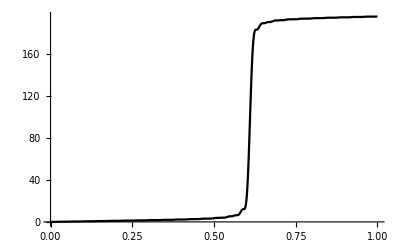

```mathematica
aa12=Transpose[{b,a12}];
q12=ListPlot[aa12,Joined->True,PlotRange->All,PlotStyle->Black]
```

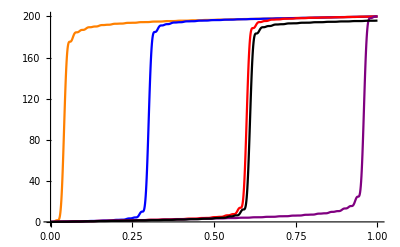

```mathematica
Show[q3,q10,q11,q9,q12]
```

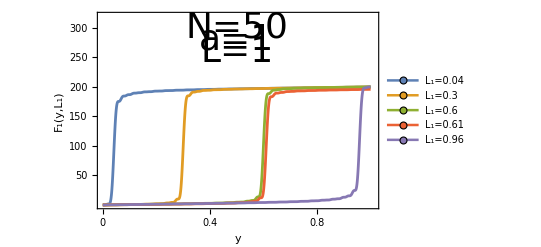

{{0.1,1},{0.2,2},{0.3,3}}

```mathematica
ListPlot[{aa3,aa10,aa11,aa12,aa9},Joined->True,PlotStyle->Thickness[0.005],Frame->{True, True, True, True}, FrameTicks->{{{50,100,150,200,250,300},None},{{0,0.2, 0.4, 0.6, 0.8,1.0},None}}, PlotRange->{{0,1.01},{0,320}},FrameLabel->{{"F_1(y,L_1)", None},{"y", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,32],PlotLegends->Placed[PointLegend[{"L_1=0.04","L_1=0.3","L_1=0.6","L_1=0.61","L_1=0.96"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Top}],Epilog->{Text[Style["N=50",Directive[Black,36]],{0.5,300}],Text[Style["a=1",Directive[Black,36]],{0.5,280}],Text[Style["L=1",Directive[Black,36]],{0.5,260}]}]
```